# Cubic best-approximation interpolating splines for RealSolarSystem

## ISA model

## Atmosphere model.

### Constants (SI units).

```mathematica
g0=9.80665;
Rstar=8.31432;
Mair=0.0289644;
atm=101325;
Celsius0=273.15;
meanEarthRadius=6371009;
km=1000;
```

```mathematica
geopotentialHeight[h_]:=(meanEarthRadius h)/(meanEarthRadius+h)
```

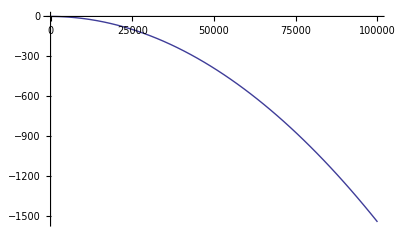

```mathematica
Plot[geopotentialHeight[h]-h,{h,0,100000}]
```

### Barometric formula.

```mathematica
barometricPressure[Pb_,Tb_,Lb_,h_,hb_]:=
Piecewise[{{Pb(Tb/(Tb+Lb(h-hb)))^((g0 Mair)/(Rstar Lb)), Lb≠0}, {Pb ⅇ^((-g0 Mair(h-hb))/(Rstar Tb)), Lb==0}}]
```

### International Standard Atmosphere (1976)—extended above the mesopause by careful eyeballing from a graph of dubious provenance.

#### Temperature as a function of geopotential altitude:

```mathematica
TTroposphere[h_]:=
15+Celsius0-6.5h/km;
TTropopause[h_]:=
TTroposphere[11000];
TLowStratosphere[h_]:=
TTropopause[20000]+(h-20000)/km;
THighStratosphere[h_]:=
TLowStratosphere[32000]+2.8(h-32000)/km;
TStratopause[h_]:=
THighStratosphere[47000];
TLowMesosphere[h_]:=
TStratopause[51000]-2.8(h-51000)/km;
THighMesosphere[h_]:=
TLowMesosphere[71000]-2.0(h-71000)/km;
TMesopause[h_]:=
THighMesosphere[84852]
TThermosphere[h_]:=
TMesopause[90000]+(h-90000)/km
```

```mathematica
TGeopot[h_]:=Piecewise[{{TTroposphere[h], 0≤h<11000}, {TTropopause[h], 11000≤h<20000}, {TLowStratosphere[h], 20000≤h<32000}, {THighStratosphere[h], 32000≤h<47000}, {TStratopause[h], 47000≤h<51000}, {TLowMesosphere[h], 51000≤h<71000}, {THighMesosphere[h], 71000≤h<84852}, {TMesopause[h], 84852≤h<90000}, {TThermosphere[h], 90000≤h}}]
```

```mathematica
T[h_]:=TGeopot[geopotentialHeight[h]];
```

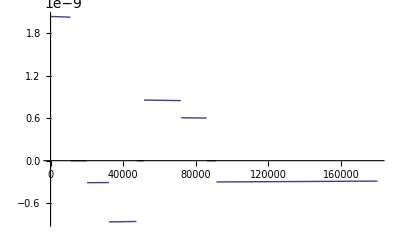

```mathematica
Plot[T''[h],{h,0,180km}]
```

### Pressure as a function of geopotential altitude.

```mathematica
pTroposphere[h_]:=barometricPressure[
101325,TTroposphere[0],-6.5/1000,h,0];
pTropopause[h_]:=barometricPressure[
pTroposphere[11000],TTropopause[11000],
0./1000,h,11000];
pLowStratosphere[h_]:=barometricPressure[
pTropopause[20000],TLowStratosphere[20000],
1/1000,h,20000];
pHighStratosphere[h_]:=barometricPressure[
pLowStratosphere[32000],THighStratosphere[32000],
2.8/1000,h,32000];
pStratopause[h_]:=barometricPressure[
pHighStratosphere[47000],TStratopause[47000],
0/1000,h,47000];
pLowMesosphere[h_]:=barometricPressure[
pStratopause[51000],TLowMesosphere[51000],
-2.8/1000,h,51000];
pHighMesosphere[h_]:=barometricPressure[
pLowMesosphere[71000],THighMesosphere[71000],
-2.0/1000,h,71000];
pMesopause[h_]:=barometricPressure[
pHighMesosphere[84852],TMesopause[84852],
-2.0/1000,h,84852];
pThermosphere[h_]:=barometricPressure[
pMesopause[90000],TThermosphere[90000],
1/1000,h,90000];
```

```mathematica
pGeopot[h_]:=Piecewise[{{pTroposphere[h], 0≤h<11000}, {pTropopause[h], 11000≤h<20000}, {pLowStratosphere[h], 20000≤h<32000}, {pHighStratosphere[h], 32000≤h<47000}, {pStratopause[h], 47000≤h<51000}, {pLowMesosphere[h], 51000≤h<71000}, {pHighMesosphere[h], 71000≤h<84852}, {pMesopause[h], 84852≤h<90000}, {pThermosphere[h], 90000≤h}}]
```

```mathematica
boundsGeopot={
0,11000,20000,32000,47000,
51000,71000,84852,90000};
```

```mathematica
pLayers=Composition[#,geopotentialHeight]&/@{pTroposphere,pTropopause,pLowStratosphere,pHighStratosphere,pStratopause,pLowMesosphere,pHighMesosphere,pMesopause,pThermosphere};
```

### Pressure as a function of geometric altitude.

```mathematica
p[h_]:=pGeopot[geopotentialHeight[h]]
```

```mathematica
bounds=Append[
h/@boundsGeopot /.
NSolve[geopotentialHeight[h/@boundsGeopot]==
boundsGeopot]⟦1⟧,
180km
];
Clear[h]
```

### Temperature utilities

```mathematica
TLayers=Composition[#,geopotentialHeight]&/@{TTroposphere,TTropopause,TLowStratosphere,THighStratosphere,TStratopause,TLowMesosphere,THighMesosphere,TMesopause,TThermosphere};
```

### Visualisations.

#### Temperature.

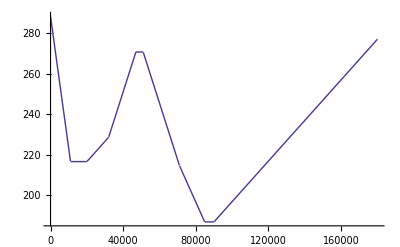

```mathematica
Plot[TGeopot[h],{h,0,180km}]
```

#### Plots of P (logarithmic and linear), ⅆP/ⅆh, (ⅆ^2 P)/(ⅆ h^2), (ⅆ^2 P)/(ⅆ h^2), (ⅆ^3 P)/(ⅆ h^3), (ⅆ^4 P)/(ⅆ h^4), (|1/((ⅆ^4 P)/(ⅆ h^4))|)^(1/4).

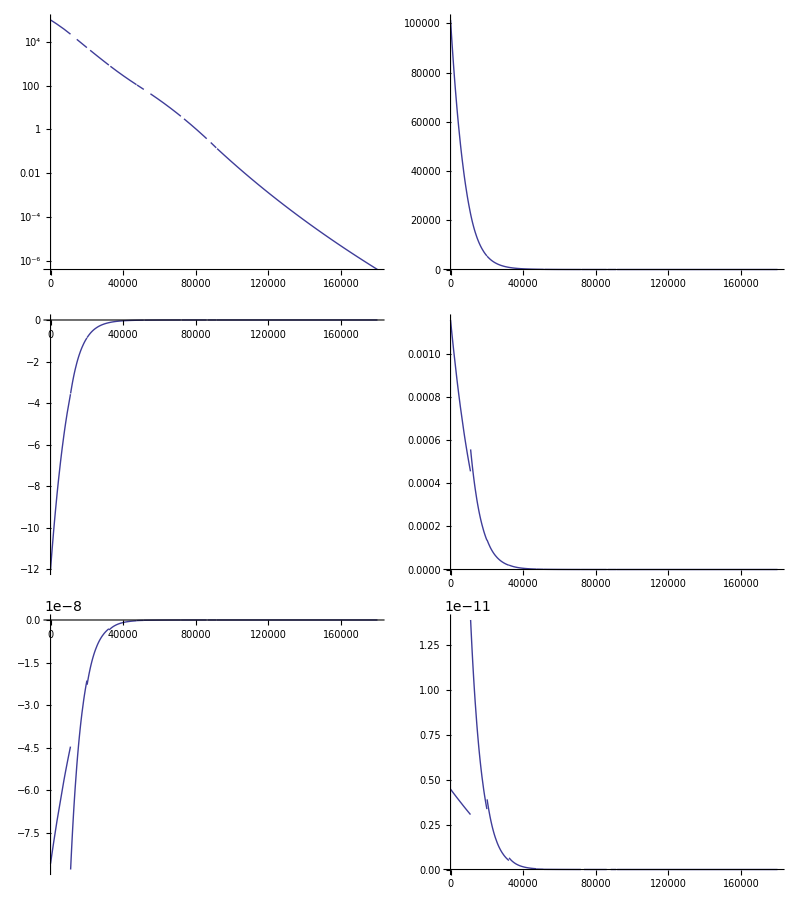

```mathematica
TableForm[Partition[
{LogPlot[p[h],{h,0,180000},PlotRange->Full],
Plot[p[h],{h,0,180000},PlotRange->Full],
Plot[p'[h],{h,0,180000},PlotRange->Full],
Plot[p''[h],{h,0,180000},PlotRange->Full],
Plot[p'''[h],{h,0,180000},PlotRange->Full],
Plot[p''''[h],{h,0,180000},PlotRange->Full],
Plot[1/p''''[h]^(1/4),{h,0,180000},PlotRange->Full]
},2]]
```

#### The step length heuristic, (|P/((ⅆ^4 P)/(ⅆ h^4))|)^(1/4).

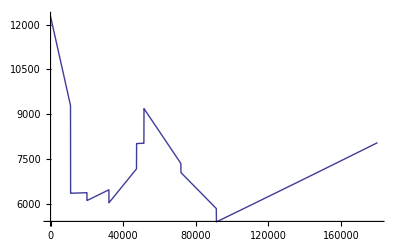

```mathematica
Plot[(p[h]/p''''[h])^(1/4),{h,0,180000},PlotRange->Full]
```

## RSS v6 model (Starwaster, 2014-03-17, in commit ).

```mathematica
rssString="key =	0	1.00074938005159	0	-0.112932216731154
			key =	1	0.887817163320432	-0.112932216731154	-0.102383696800236
			key =	2	0.785433466520196	-0.102383696800236	-0.092606079428248
			key =	3	0.692827387091948	-0.092606079428248	-0.083559421640834
			key =	4	0.609267965451115	-0.083559421640834	-0.075204960098835
			key =	5	0.53406300535228	-0.075204960098835	-0.067505103824342
			key =	6	0.466557901527938	-0.067505103824342	-0.060423426793117
			key =	7	0.406134474734821	-0.060423426793117	-0.053924660387524
			key =	8	0.352209814347297	-0.053924660387524	-0.047974685703597
			key =	9	0.3042351286437	-0.047974685703597	-0.042540525705509
			key =	10	0.261694602938191	-0.042540525705509	-0.037590337220107
			key =	11	0.224104265718084	-0.037590337220107	-0.032471289833586
			key =	12	0.191632975884499	-0.032471289833586	-0.027843493592706
			key =	13	0.163789482291792	-0.027843493592706	-0.02379794698535
			key =	14	0.139991535306442	-0.02379794698535	-0.020340201879907
			key =	15	0.119651333426536	-0.020340201879907	-0.017384853103928
			key =	16	0.102266480322608	-0.017384853103928	-0.014858904509876
			key =	17	0.087407575812732	-0.014858904509876	-0.012699965994175
			key =	18	0.074707609818557	-0.012699965994175	-0.010854712482068
			key =	19	0.063852897336488	-0.010854712482068	-0.009277566815723
			key =	20	0.054575330520766	-0.009277566815723	-0.005936489407756
			key =	25	0.024892883481984	-0.005936489407756	-0.002686584679796
			key =	30	0.011459960083005	-0.002686584679796	-0.001167830800293
			key =	35	0.005620806081539	-0.001167830800293	-0.00040944307168
			key =	45	0.001526375364736	-0.00040944307168	-0.000105243424372
			key =	55	0.00047394112102	-0.000105243424372	-0.00003098333627
			key =	65	0.000164107758324	-0.00003098333627	-0.00001019066441
			key =	75	0.000062201114229	-0.00001019066441	-0.000003675860762
			key =	85	0.000025442506612	-0.000003675860762	-0.000001196261407
			key =	100	0.000007498585506	-0.000001196261407	-0.000000394672641
			key =	110	0.0000035518591	-0.000000394672641	-0.000000179020197
			key =	120	0.000001761657127	-0.000000179020197	-0.000000085162644
			key =	130	0.000000910030685	-0.000000085162644	-0.00000004225905
			key =	140	0.000000487440187	-0.00000004225905	-0.000000021773993
			key =	150	0.000000269700262	-0.000000021773993	-0.000000011604662
			key =	160	0.000000153653645	-0.000000011604662	-0.000000006376405
			key =	170	0.000000089889599	-0.000000006376405	-0.00000000898896
			key =	180	0	-0.00000000898896	0";
```

```mathematica
rssRaw=ToExpression["{"~~StringReplace[rssString,{"\n"->"},\n","\t\t\t"->"","\t"->",","key =\t"->"{"}]~~"}}"];
```

```mathematica
xL=1000rssRawᵀ⟦1⟧;
yL=rssRawᵀ⟦2⟧*atm;
tgLin=rssRawᵀ⟦3⟧*atm/km;
tgLout=rssRawᵀ⟦4⟧*atm/km;
```

## Spline computations.

### Utilities.

```mathematica
Clear[steps,fixedSteps];
zero[f_,lo_,hi_,ε_]:=
Module[
{x=(lo+hi)/2,xlo=lo,xhi=hi},
If[f[hi]≤0||f[lo]≥0,Print["INVALID BISECTION"]];
While[Abs[f[x]]>ε,
If[f[x]>0,
xhi=x,
xlo=x
];x=(xlo+xhi)/2
];x
];
fixedSteps[α_,p_,lo_,hi_,N_,heuristic_]:=
Union[
Module[
{xs={lo}},
Table[
AppendTo[xs,Last[xs]+α heuristic[p,Last[xs]]],
{i,1,N}
];
xs
]
];
steps[p_,lo_,hi_,N_,heuristic_:(Abs[#1[#2]/Derivative[4][#1][#2]]^(1/4)&)]:=
fixedSteps[
zero[Last[fixedSteps[#,p,lo,hi,N,heuristic]]-hi&,.00001,100,(hi-lo)1*^-12],
p,lo,hi,N,heuristic]
```

```mathematica
Needs["FunctionApproximations`"];
Quiet[Needs["Combinatorica`"]];
SymPart[l_List,spec_?NumberQ]:=l[[spec]];
SymBS[l_List?(NumberQ[Total[#]]&),k_]:=BinarySearch[l,k]
approximation[xs_,ys_,outTangents_,inTangents_]:=Function[
h,
With[
{i=Floor[SymBS[xs,h]]},
With[
{t=If[i<Length[xs],(h-SymPart[xs,i])/(SymPart[xs,i+1]-SymPart[xs,i]),0],
Δ=SymPart[xs,i+1]-SymPart[xs,i]},
(2 t^3-3 t^2+1)SymPart[ys,i]+
Δ(t^3-2 t^2+t)SymPart[outTangents,i]+
If[i<Length[ys],
(-2 t^3+3 t^2)SymPart[ys,i+1]+
Δ(t^3-t^2)SymPart[inTangents,i+1],
0
]
]
]
]
```

```mathematica
bestContinuousInterpolatingPiecewiseCubic[f_,x_,h_,ε_]:=Table[Expand[MiniMaxApproximation[(f[h]-(f[x⟦i⟧]+((f[x⟦i+1⟧]-f[x⟦i⟧]) (h-x⟦i⟧))/(x⟦i+1⟧-x⟦i⟧)))/((h-x⟦i⟧) (h-x⟦i+1⟧)),{h,{x⟦i⟧+ε (x⟦i+1⟧-x⟦i⟧),x⟦i+1⟧-ε (x⟦i+1⟧-x⟦i⟧)},1,0}]⟦2,1⟧ (h-x⟦i⟧) (h-x⟦i+1⟧)+(f[x⟦i⟧]+((f[x⟦i+1⟧]-f[x⟦i⟧]) (h-x⟦i⟧))/(x⟦i+1⟧-x⟦i⟧))],{i,1,Length[x]-1}
]
```

### Computation (piecewise best approximation cubic interpolating, cubic Hermite interpolating).

```mathematica
ε=1*^-6;
```

```mathematica
100(bounds ⟦2;;⟧-bounds⟦;;-2⟧)/bounds⟦-1⟧//Round
```

{6,5,7,8,2,11,8,3,49}

```mathematica
stepCounts={4,5,7,9,2,9,9,4,51};
stepCounts//Total
```

100

```mathematica
Quiet[
xxH=Table[
steps[pLayers⟦i⟧,bounds⟦i⟧,bounds⟦i+1⟧,stepCounts⟦i⟧],
{i,1,Length[pLayers]}
];
]
polyH=Table[
bestContinuousInterpolatingPiecewiseCubic[
pLayers⟦i⟧,xxH⟦i⟧,h,ε],
{i,1,Length[pLayers]}
];
dPolyH=D[polyH,h];
tgHin=Prepend[Join@@Table[
Table[dPolyH⟦i,j-1⟧/.h->xxH⟦i,j⟧,{j,2,Length[xxH⟦i⟧]}],
{i,1,Length[pLayers]}
],p'[xxH⟦1,1⟧]];
tgHout=Append[Join@@Table[
Table[dPolyH⟦i,j⟧/.h->xxH⟦i,j⟧,{j,1,Length[xxH⟦i⟧]-1}],
{i,1,Length[pLayers]}
],p'[xxH⟦-1,-1⟧]];
xH=Append[Union@@xxH⟦;;,;;-2⟧,xxH⟦-1,-1⟧];
yH=p/@xH;
tgH=p'/@xH;
```

```mathematica
stepCountsHH={8,11,15,18,4,19,17,7,101};
```

```mathematica
Quiet[
xxHH=Table[
steps[pLayers⟦i⟧,bounds⟦i⟧,bounds⟦i+1⟧,stepCountsHH⟦i⟧],
{i,1,Length[pLayers]}
];
]
polyHH=Table[
bestContinuousInterpolatingPiecewiseCubic[
pLayers⟦i⟧,xxHH⟦i⟧,h,ε],
{i,1,Length[pLayers]}
];
dPolyHH=D[polyHH,h];
tgHHin=Prepend[Join@@Table[
Table[dPolyHH⟦i,j-1⟧/.h->xxHH⟦i,j⟧,{j,2,Length[xxHH⟦i⟧]}],
{i,1,Length[pLayers]}
],p'[xxHH⟦1,1⟧]];
tgHHout=Append[Join@@Table[
Table[dPolyHH⟦i,j⟧/.h->xxHH⟦i,j⟧,{j,1,Length[xxHH⟦i⟧]-1}],
{i,1,Length[pLayers]}
],p'[xxHH⟦-1,-1⟧]];
xHH=Append[Union@@xxHH⟦;;,;;-2⟧,xxHH⟦-1,-1⟧];
yHH=p/@xHH;
tgHH=p'/@xHH;
```

## Error plots.

Colouring:
Piecewise Hermite interpolation (100 points),
Piecewise best approximation (100 points),
Piecewise Hermite interpolation (200 points),
Piecewise best approximation (200 points),
RSS v6.

### Relative error plots.

#### Logarithmic magnitude of the relative error.

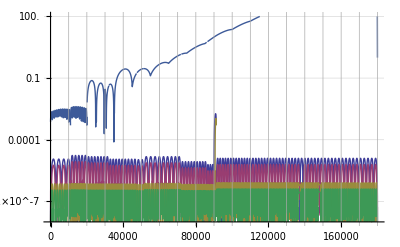

```mathematica
LogPlot[{
Abs[(approximation[xH,yH,tgH,tgH][h])/p[h]-1],
Abs[(approximation[xH,yH,tgHout,tgHin][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHH,tgHH][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHHout,tgHHin][h])/p[h]-1],

Abs[(approximation[xL,yL,tgLout,tgLin][h])/p[h]-1]},
{h,0,Last[xH]},PlotRange->{1*^-8,100},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,190km,10000],10.^Range[-13,2]},
GridLines->{Range[0,190km,10km],Flatten@Outer[Times,10.^Range[-13,2],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray
]
```

#### A closer look at the troposphere and stratosphere, where the RSS v6 model isn’t completely insane.

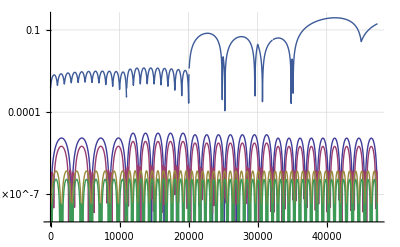

```mathematica
LogPlot[{
Abs[(approximation[xH,yH,tgH,tgH][h])/p[h]-1],
Abs[(approximation[xH,yH,tgHout,tgHin][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHH,tgHH][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHHout,tgHHin][h])/p[h]-1],

Abs[(approximation[xL,yL,tgLout,tgLin][h])/p[h]-1]},
{h,0,47349.303740712574},PlotRange->{1*^-8,.31},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,xH⟦-1⟧,1000],10.^Range[-13,2]},
GridLines->{Range[0,xH⟦-1⟧,1000],Flatten@Outer[Times,10.^Range[-13,2],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray
]
```

#### Magnitude of the relative error.

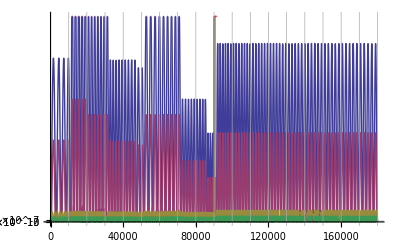

```mathematica
Plot[{
Abs[(approximation[xH,yH,tgH,tgH][h])/p[h]-1],
Abs[(approximation[xH,yH,tgHout,tgHin][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHH,tgHH][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHHout,tgHHin][h])/p[h]-1]},
{h,0,xH//Last},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,180km,10000],10.^Range[-13,2]},
GridLines->{Range[0,180km,10000],Flatten@Outer[Times,10.^Range[-13,2],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

#### Magnitude of the relative error (100-step and 200-step, side by side)

200 points allows us to better even out the errors between the exponential chunks of the ISA model.

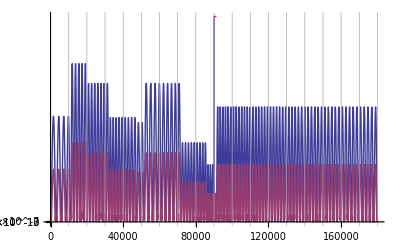
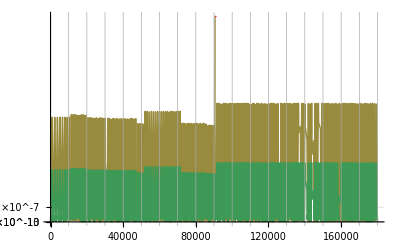

```mathematica
Row[{
Plot[{
Abs[(approximation[xH,yH,tgH,tgH][h])/p[h]-1],
Abs[(approximation[xH,yH,tgHout,tgHin][h])/p[h]-1]},
{h,0,xH//Last},PlotStyle->Thick,
ImageSize->Scaled[.4],Ticks->{Range[0,180km,10000],10.^Range[-13,2]},
GridLines->{Range[0,180km,10000],Flatten@Outer[Times,10.^Range[-13,2],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
],
Plot[{
Abs[(approximation[xHH,yHH,tgHH,tgHH][h])/p[h]-1],
Abs[(approximation[xHH,yHH,tgHHout,tgHHin][h])/p[h]-1]},
{h,0,xH//Last},PlotStyle->{{Thick,ColorData[1][3]},{ColorData[1][4]}},
ImageSize->Scaled[.4],Ticks->{Range[0,180km,10000],10.^Range[-13,2]},
GridLines->{Range[0,180km,10000],Flatten@Outer[Times,10.^Range[-13,2],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]}]
```

#### Relative error.

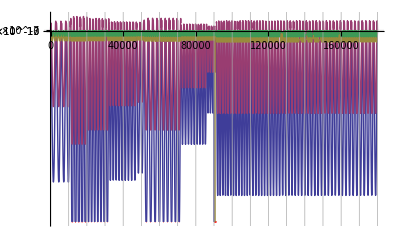

```mathematica
Plot[{
(approximation[xH,yH,tgH,tgH][h])/p[h]-1,
(approximation[xH,yH,tgHout,tgHin][h])/p[h]-1,
(approximation[xHH,yHH,tgHH,tgHH][h])/p[h]-1,
(approximation[xHH,yHH,tgHHout,tgHHin][h])/p[h]-1},
{h,0,xH//Last},PlotStyle->{Thick},
ImageSize->Full,Ticks->{Range[0,180km,10000],Flatten[{#,-#}&/@(10.^Range[-13,2])]},
GridLines->{Range[0,180km,10000],Flatten[{#,-#}&/@Outer[Times,10.^Range[-13,2],Range[1,9,1]]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

### Absolute error plots.

#### Logarithmic magnitude of the absolute error.

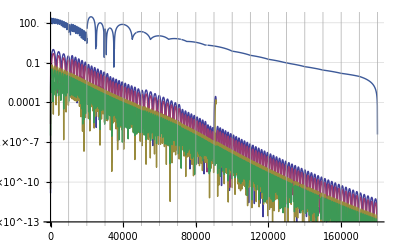

```mathematica
LogPlot[{
Abs[approximation[xH,yH,tgH,tgH][h]-p[h]],
Abs[approximation[xH,yH,tgHout,tgHin][h]-p[h]],
Abs[approximation[xHH,yHH,tgHH,tgHH][h]-p[h]],
Abs[approximation[xHH,yHH,tgHHout,tgHHin][h]-p[h]],
Abs[approximation[xL,yL,tgLout,tgLin][h]-p[h]]},
{h,First[xH],Last[xH]},PlotRange->{1*^-13,300},PlotStyle->{Thick},
ImageSize->Full,Ticks->{Range[0,180km,10km],Flatten[{#,-#}&/@(10.^Range[-13,2])]},
GridLines->{Range[0,180km,10km],Flatten[{#,-#}&/@Outer[Times,10.^Range[-13,2],Range[1,9,1]]]},
GridLinesStyle->Lighter@Gray
]
```

## Output.

### Utilities.

```mathematica
keyFrames[x_,y_,tgin_,tgout_]:=StringReplace[
ToString[
TableForm[
Map[
ToString[CForm[#]]&,
{ConstantArray["key =",Length[x]],
x,
y,
tgin,
tgout}ᵀ,{2}
]
]
],{"\""->"","\n\n"->"\n"}]
```

### Pressure keyframes for the RSS configuration file.

```mathematica
keyFrames[xHH/km,yHH/atm,tgHHin/(atm/km),tgHHout/(atm/km)]
```

key =   0.                   1.                        -0.1185604537092152        -0.11855959978771942
key =   1.5512810696042834   0.8293033334108524        -0.10183830225110932       -0.10183674646034666
key =   3.049490512617914    0.6877017510446373        -0.08747110450514875       -0.08746976950185438
key =   4.496387604836978    0.5702444163147664        -0.0751284129344817        -0.07512726633490288
key =   5.893677091578151    0.47282126627696414       -0.06452535720588375       -0.06452437241824793
key =   7.243010623061255    0.3920205567378669        -0.05541708242752019       -0.05541623726573463
key =   8.545988169576226    0.3250104789672165        -0.047593141263616516      -0.047592415333238956
key =   9.804159415369073    0.26944079326066694       -0.040872666060624986      -0.040872042882559356
key =   11.01902513031035    0.2233611050921582        -0.035100221317578735      -0.035099557970493446
key =   11.84014685339708    0.19632505252876972       -0.03084380270879462       -0.03084310345055893
key =   12.661479569463696   0.17256150402323664       -0.02710343581969091       -0.027102821588632576
key =   13.483023359760763   0.1516743473174663        -0.023816656413559647      -0.023816116576602698
key =   14.304778305580532   0.1333154167235328        -0.020928458501624652      -0.020927984178645793
key =   15.12674448825698    0.1171786895168694        -0.018390506878715605      -0.018390090023457557
key =   15.948921989165822   0.10299518481855771       -0.016160327709296325      -0.01615996154844787
key =   16.771310889724543   0.09052847993471885       -0.014200598194339229      -0.014200276408409946
key =   17.593911271392436   0.07957076941364262       -0.012478521248672299      -0.012478238370883084
key =   18.416723215670608   0.06993940112805067       -0.010965277100050496      -0.010965028558431775
key =   19.239746804102023   0.06147383164159355       -0.00963554111113529       -0.00963532275380243
key =   20.062982118274434   0.05403295010784879       -0.008467059560467996      -0.008466865633093621
key =   20.848089497565947   0.04778939820639058       -0.007459985030116664      -0.007459812291011911
key =   21.63620936661535    0.042267349078245586      -0.0065726934531660074     -0.00657254126906443
key =   22.42735394519108    0.037383419911108245      -0.00579093891910887       -0.0057908050878031645
key =   23.221535507546527   0.03306386499304308       -0.0051021685425771636     -0.00510205025182942
key =   24.018766382699184   0.029243461811422816      -0.0044953216976765225     -0.00449521773683876
key =   24.8190589547115     0.025864525910496747      -0.003960654553978478      -0.0039605627357514476
key =   25.622425662973434   0.022876039623080074      -0.0034895812227674168     -0.0034895006191361998
key =   26.42887900248672    0.02023288151260161       -0.0030745380406068013     -0.0030744671255894637
key =   27.238431524150865   0.017895144883579222      -0.0027088605245762457     -0.0027087978126772794
key =   28.05109583505088    0.01582753506445577       -0.0023866766401096145     -0.002386621463670356
key =   28.86688459874678    0.013998836357006461      -0.00210281336829757       -0.002102764823022757
key =   29.685810535564812   0.012381440599191202      -0.0018527126731341518     -0.0018526698042597327
key =   30.50788642289051    0.010950930219291178      -0.0016323587220781594     -0.0016323209889605624
key =   31.333125095463508   0.009685709482500008      -0.001438213440182944      -0.0014381801209664721
key =   32.16153944567676    0.00856667835929167       -0.001267159475800941      -0.0012671291433869782
key =   32.938227246035915   0.007641143253424154      -0.0011194443454613022     -0.001119416715203487
key =   33.72239861830024    0.006815621618893492      -0.00098894869315807       -0.0009889242507575187
key =   34.514127125411996   0.00607930403304661       -0.0008736658458577912     -0.0008736442823188312
key =   35.31348708126911    0.005422549546182163      -0.0007718223103765099     -0.0007718032220685227
key =   36.12055355892001    0.004836759353067881      -0.0006818512473742133     -0.0006818343999548707
key =   36.93540239885774    0.004314264124281222      -0.000602368599707903      -0.0006023537275719138
key =   37.758110217414796   0.0038482235201537335     -0.0005321516055926249     -0.0005321384600078337
key =   38.588754415260034   0.0034325365698691804     -0.00047012007111754727    -0.00047010846628046477
key =   39.42741318599914    0.003061761740754522      -0.0004153197608027341     -0.0004153094957067317
key =   40.274165524880075   0.002731045649879268      -0.0003669076453724236     -0.0003668985815476719
key =   41.12909123760493    0.0024360594834088893     -0.00032413902137201937    -0.00032413101651729585
key =   41.992270949249814   0.0021729422902310026     -0.0002863559791165239     -0.0002863489027220139
key =   42.86378611329412    0.0019382504065130982     -0.00025297731542709285    -0.0002529710682454082
key =   43.74371902076092    0.0017289123482408188     -0.00022348959544633097    -0.00022348406691727552
key =   44.63215280946986    0.001542188580481708      -0.00019743921339973302    -0.00019743433762356509
key =   45.52917147340433    0.0013756356360598086     -0.00017442548188152307    -0.0001744211709807741
key =   46.434859872194416   0.0012270741133522903     -0.0001540943976740258     -0.00015409058835020637
key =   47.34930374071258    0.0010945601337771134     -0.0001361332366854071     -0.0001361300999622217
key =   48.364384412817486   0.0009647618356676518     -0.00011995173663077706    -0.0001199491828070985
key =   49.379785586778326   0.0008503557210569973     -0.00010569384206786046    -0.00010569159114107088
key =   50.39550741421541    0.0007495164938529389     -0.00009313069365486576    -0.00009312871041255892
key =   51.41155004684329    0.0006606353132858362     -0.00008206084867257565    -0.00008205914602801715
key =   52.60233679755664    0.0005693036016959514     -0.00007155713957078758    -0.00007155568678730067
key =   53.77919611346216    0.0004905938576126548     -0.00006239767385386734    -0.00006239640894781644
key =   54.94228410298658    0.0004227624006014844     -0.0000544104256104594     -0.000054409320819982295
key =   56.091755284696234   0.00036430633500513854    -0.00004744540325580311    -0.00004744444130583597
key =   57.22776259968469    0.0003139303145738763     -0.000041371807283236435   -0.00004137096802618017
key =   58.35045742395875    0.0002705178923931361     -0.00003607556860149402    -0.00003607483704626997
key =   59.45998958082039    0.00023310682382008942    -0.00003145721292357758    -0.00003145657516845965
key =   60.556507353241216   0.00020086777728288698    -0.000027429992203311256   -0.000027429435582640572
key =   61.64015749622714    0.00017308598293538365    -0.000023918256528569814   -0.000023917771478660894
key =   62.711085249170246   0.00014914541394851294    -0.00002085603677190657    -0.000020855613696683044
key =   63.76943434818539    0.00012851515108212665    -0.00001818580287864788    -0.00001818543442226444
key =   64.815347038429      0.00011073762934697615    -0.000015857387455682573   -0.000015857065686591502
key =   65.84896408639746    0.00009541850709542147    -0.000013827041357366145   -0.000013826760859805913
key =   66.8704247922031     0.00008221793368536839    -0.000012056614537032086   -0.000012056370038392204
key =   67.87986700182476    0.00007084302273310274    -0.000010512838560751086   -0.000010512625468395554
key =   68.8774271193317     0.00006104136458678227    -9.166702602146737e-6      -9.16651697825816e-6
key =   69.86324011907763    0.000052595434599546184   -7.992908453558665e-6      -7.99274660841423e-6
key =   70.8374395578637     0.00004531777356493782    -6.969395258678345e-6      -6.969253895473243e-6
key =   71.80015758707647    0.000039046833733439246   -6.076925603873962e-6      -6.076804772790693e-6
key =   72.68865461815959    0.00003398575432010344    -5.330948534717209e-6      -5.330845145916447e-6
key =   73.57022854353788    0.000029580547160393628   -4.676538578623587e-6      -4.676447927603061e-6
key =   74.44493098881618    0.000025746233592392944   -4.102454926858646e-6      -4.102375481234327e-6
key =   75.31281323119997    0.000022408843008637936   -3.5988387258317427e-6     -3.598768870482683e-6
key =   76.17392620126307    0.00001950398719402563    -3.1570408681075038e-6     -3.1569798751603056e-6
key =   77.02832048471646    0.00001697561926004407    -2.7694742556909047e-6     -2.769420486182663e-6
key =   77.87604632417766    0.000014774953279356489   -2.429482135652753e-6      -2.4294350158398353e-6
key =   78.71715362094046    0.00001285952381730844    -2.1312254357726504e-6     -2.1311841056792775e-6
key =   79.551691936745      0.000011192367249356912   -1.8695813146192711e-6     -1.8695450373390193e-6
key =   80.37971049554787    9.741309097476518e-6      -1.6400558045349966e-6     -1.6400240307869246e-6
key =   81.20125818529202    8.478343659349097e-6      -1.4387065426054444e-6     -1.4386785891349887e-6
key =   82.01638355967633    7.379093980827345e-6      -1.2620747763849974e-6     -1.2620502652020841e-6
key =   82.82513483992473    6.422341768933253e-6      -1.1071265718097054e-6     -1.1071051142141048e-6
key =   83.62755991655452    5.589618189260209e-6      -9.712002904574998e-7      -9.71181448483281e-7
key =   84.42370635114384    4.864847663982511e-6      -8.519608581116953e-7      -8.51944338109559e-7
key =   85.2136213780981     4.234037807288761e-6      -7.473599370498319e-7      -7.473454667471942e-7
key =   85.99735190641914    3.6850095235747807e-6     -6.556005771082963e-7      -6.55587954868776e-7
key =   86.77126507788661    3.2092787757787186e-6     -5.754642912975324e-7      -5.75453268314719e-7
key =   87.53914411678717    2.794954292752292e-6      -5.051226323794921e-7      -5.051129705129523e-7
key =   88.30103431720043    2.4341112574484694e-6     -4.4337850910771023e-7     -4.4337003053471976e-7
key =   89.05698066083089    2.119847408523293e-6      -3.8918117164669293e-7     -3.8917373913668035e-7
key =   89.80702781872314    1.846151123042689e-6      -3.4160827520346016e-7     -3.416017290173781e-7
key =   90.55122015297522    1.6077865140798708e-6     -2.998501678608832e-7      -2.9984441920604384e-7
key =   91.28960171845002    1.4001933490614182e-6     -2.6319616869285707e-7     -2.486952005932888e-7
key =   92.00550873461046    1.2333118599412074e-6     -2.1819956067829382e-7     -2.1819399765406504e-7
key =   92.72423273172485    1.0863213945314536e-6     -1.9143856792449206e-7     -1.9143367699672882e-7
key =   93.44578535382313    9.568509390520772e-7      -1.6795972868642057e-7     -1.679554483744513e-7
key =   94.17017829735393    8.428121226896023e-7      -1.4736050239941215e-7     -1.473567449209859e-7
key =   94.89742331145317    7.423655223488129e-7      -1.2928769638390706e-7     -1.2928439701265594e-7
key =   95.62753219821417    6.538909846164284e-7      -1.1343144740828045e-7     -1.134285511429241e-7
key =   96.3605168129594     5.759614859695728e-7      -9.951989504709977e-8      -9.95173584899587e-8
key =   97.09638906451391    5.073201093718896e-7      -8.731453760845615e-8      -8.73123057928803e-8
key =   97.83516091548039    4.46859765699811e-7       -7.660609906427105e-8      -7.660414409027002e-8
key =   98.57684438251582    3.936053327437919e-7      -6.721099425878047e-8      -6.720928192049638e-8
key =   99.32145153660994    3.466979235488415e-7      -5.896815235791663e-8      -5.8966646584020774e-8
key =   100.0689945033653    3.053810302255262e-7      -5.1736241448129367e-8     -5.173491910923864e-8
key =   100.81948546327908   2.6898831963163175e-7     -4.539127656936708e-8      -4.5390118869270026e-8
key =   101.57293665202647   2.3693288398456065e-7     -3.982448055650987e-8      -3.982346454334898e-8
key =   102.32936036074604   2.0869777294549137e-7     -3.4940411954074005e-8     -3.493952204123044e-8
key =   103.08876893632655   1.838276543975248e-7      -3.06553395600465e-8       -3.0654556031009224e-8
key =   103.85117478169572   1.6192146935538855e-7     -2.689579529450524e-8      -2.6895108609656207e-8
key =   104.61659035611073   1.426259624876361e-7      -2.3597329116220923e-8     -2.3596726899186627e-8
key =   105.38502817545033   1.2562998386281498e-7     -2.070339136635255e-8      -2.070286293924818e-8
key =   106.15650081250897   1.1065946997674138e-7     -1.8164369129178214e-8     -1.8163906411457024e-8
key =   106.9310208972926    9.747302307980794e-8      -1.593673553266452e-8      -1.593632957429027e-8
key =   107.70860111731623   8.585801747804816e-8      -1.3982299517997457e-8     -1.3981941938454638e-8
key =   108.4892542179035    7.562716998532403e-8      -1.2267554609866885e-8     -1.2267240569173477e-8
key =   109.27299300248785   6.661551919379164e-8      -1.076310461319652e-8      -1.0762830152965702e-8
key =   110.05983033291581   5.867776482658846e-8      -9.443159955895734e-9      -9.4429192202336e-9
key =   110.84977912975185   5.168592424694919e-8      -8.28509192107281e-9       -8.284880967146415e-9
key =   111.64285237258542   4.552726831549305e-8      -7.269047652113642e-9      -7.268861865960066e-9
key =   112.43906310033962   4.010250329483534e-8      -6.377608557329834e-9      -6.3774461283796e-9
key =   113.23842441158197   3.532416947066346e-8      -5.595493791526083e-9      -5.59535127707469e-9
key =   114.04094946483697   3.1115230655123596e-8     -4.9092955575989594e-9     -4.909170545557526e-9
key =   114.84665147890068   2.740783181815693e-8      -4.3072507109624235e-9     -4.3071406919610695e-9
key =   115.65554373315715   2.4142204805057678e-8     -3.7790381927874045e-9     -3.778941838062271e-9
key =   116.46763956789694   2.1265704487747348e-8     -3.315603840776064e-9      -3.315519144373566e-9
key =   117.28295238463754   1.8731959801643352e-8     -2.909002997779728e-9      -2.9089289141697117e-9
key =   118.10149564644574   1.6500125973500722e-8     -2.5522660046340328e-9     -2.552200839725792e-9
key =   118.92328287826211   1.4534225878138631e-8     -2.2392772678887408e-9     -2.239220082924367e-9
key =   119.74832766722746   1.2802569899865155e-8     -1.964671764606749e-9      -1.9646216869169834e-9
key =   120.57664366301124   1.1277244940900727e-8     -1.7237423517032067e-9     -1.7236984216421938e-9
key =   121.40824457814219   9.933664334603154e-9      -1.5123590509328848e-9     -1.5123204615818876e-9
key =   122.2431441883408    8.750171403809505e-9      -1.326898375254258e-9      -1.3268644348883113e-9
key =   123.08135633285417   7.707690270003333e-9      -1.1641812419707625e-9     -1.1641515388873978e-9
key =   123.92289491479256   6.7894182812367484e-9     -1.0214185504153104e-9     -1.021392572809208e-9
key =   124.7677739014685    5.980555098096755e-9      -8.961632199478459e-10     -8.961404106466935e-10
key =   125.61600732473762   5.268064068329123e-9      -7.862682022129306e-10     -7.862480762281916e-10
key =   126.46760928134195   4.640462041568822e-9      -6.898496745700762e-10     -6.898321179137454e-10
key =   127.32259393325515   4.087634234370453e-9      -6.052551118185885e-10     -6.052396439440843e-10
key =   128.18097550803      3.6006711597960495e-9     -5.310344061653454e-10     -5.310208297746401e-10
key =   129.0427682991481    3.171724991706807e-9      -4.659153750150121e-10     -4.659035126174821e-10
key =   129.90798666637178   2.7938830473793276e-9     -4.08781908703883e-10      -4.08771478024948e-10
key =   130.7766450360982    2.461056348167078e-9      -3.586546789530001e-10     -3.586455122851607e-10
key =   131.64875790171564   2.167881461118848e-9      -3.1467448386623625e-10    -3.1466643941650315e-10
key =   132.52433982396218   1.9096340386672714e-9     -2.760875109002025e-10     -2.7608048640960875e-10
key =   133.4034054312866    1.6821526621691311e-9     -2.422324130818198e-10     -2.422262147221923e-10
key =   134.28596942021136   1.4817717612582223e-9     -2.1252885851739006e-10    -2.1252344224971152e-10
key =   135.17204655569842   1.3052625273415275e-9     -1.8646778008939614e-10    -1.8646303431174026e-10
key =   136.06165167151667   1.149780868494151e-9      -1.6360249304130826e-10    -1.6359832895033542e-10
key =   136.9547996706124    1.0128215665635313e-9     -1.4354110044370613e-10    -1.4353742247124066e-10
key =   137.8515055254816    8.921778973149445e-10     -1.259397403316904e-10     -1.2593652233520667e-10
key =   138.75178427854485   7.859060625484956e-10     -1.104967631349645e-10     -1.1049393456194306e-10
key =   139.6556510425247    6.922938607161996e-10     -9.694747706774628e-11     -9.694500988836427e-11
key =   140.56312100082533   6.09833090916068e-10      -8.505967791134393e-11     -8.505750933931027e-11
key =   141.47420940791469   5.371952453424906e-10     -7.462961018742898e-11     -7.462769981656357e-11
key =   142.38893158970896   4.732100982986395e-10     -6.547851118042345e-11     -6.547684368617612e-11
key =   143.3073029439597    4.168468465829776e-10     -5.744955662281224e-11     -5.7448088486878884e-11
key =   144.22933894064346   3.671974972015254e-10     -5.040513169452915e-11     -5.040384756661839e-11
key =   145.15505512235356   3.234622345933982e-10     -4.4224515069882136e-11    -4.422338638786745e-11
key =   146.0844671046949    2.8493653147468415e-10    -3.88017761245299e-11      -3.880078803092987e-11
key =   147.017590576681     2.5099979551865794e-10    -3.404398566830358e-11     -3.404311651075543e-11
key =   147.9544413011336    2.2110536885300994e-10    -2.986959908335178e-11     -2.986883568628309e-11
key =   148.895035115085     1.9477171916586073e-10    -2.620707893071936e-11     -2.620640924310837e-11
key =   149.83938793018282   1.7157468042414262e-10    -2.2993658533612386e-11    -2.299307096473485e-11
key =   150.78751573309765   1.5114061812990165e-10    -2.0174266373207763e-11    -2.0173752650523618e-11
key =   151.73943458593294   1.3314040894531616e-10    -1.7700588075511552e-11    -1.7700135192555592e-11
key =   152.69516062663794   1.1728413764612875e-10    -1.5530227719501764e-11    -1.55298307087732e-11
key =   153.65471006942323   1.0331642592731239e-10    -1.3625993693520843e-11    -1.3625647313417621e-11
key =   154.61809920517865   9.101231777083398e-11     -1.195525487829176e-11     -1.1954949122579921e-11
key =   155.58534440189447   8.017365505741884e-11     -1.0489376555386223e-11    -1.0489108389627964e-11
key =   156.55646210508482   7.062588500703516e-11     -9.20323991640719e-12      -9.203005428364908e-12
key =   157.5314688382143    6.221524799385088e-11     -8.074805705209974e-12     -8.074599349924489e-12
key =   158.51038120312697   5.480630041286311e-11     -7.08473554143093e-12      -7.0845542538637285e-12
key =   159.49321588047854   4.8279732676118466e-11    -6.2160628033143375e-12    -6.2159047891625916e-12
key =   160.47998963017102   4.25304471736388e-11      -5.4539036270954505e-12    -5.453764557808936e-12
key =   161.47071929179063   3.7465865224365877e-11    -4.785196076386637e-12     -4.785073908810809e-12
key =   162.46542178504822   3.3004435733348155e-11    -4.1984815792356605e-12    -4.1983745283769796e-12
key =   163.46411411022274   2.9074321522450202e-11    -3.683706563091199e-12     -3.683612355030496e-12
key =   164.4668133486077    2.5612242165515882e-11    -3.2320494760803846e-12    -3.2319674105206833e-12
key =   165.4735366629604    2.2562454681306163e-11    -2.835771964959891e-12     -2.835699374640052e-12
key =   166.48430129795432   1.9875855659365853e-11    -2.4880826010150204e-12    -2.488018919485026e-12
key =   167.49912458063434   1.750919035102187e-11     -2.183023910081614e-12     -2.1829684215361883e-12
key =   168.5180239208751    1.542435598158708e-11     -1.915369291207526e-12     -1.915320261046157e-12
key =   169.54101681184216   1.3587788058277363e-11    -1.6805317497743288e-12    -1.680488922352042e-12
key =   170.5681208304566    1.1969919785852967e-11    -1.4744879599724844e-12    -1.4744501946593233e-12
key =   171.59935363786235   1.054470588013509e-11     -1.2937070494689333e-12    -1.2936740139551017e-12
key =   172.6347329798968    9.289203107288329e-12     -1.1350916457412244e-12    -1.1350626946869318e-12
key =   173.67427668756457   8.183200790861963e-12     -9.959239255491945e-13     -9.95898542977519e-13
key =   174.71800267751422   7.208895333755879e-12     -8.738194000657575e-13     -8.737970230998723e-13
key =   175.76592895251846   6.350603511516141e-12     -7.666857284216306e-13     -7.666662249939894e-13
key =   176.81807360195734   5.594509918095206e-12     -6.726875605074617e-13     -6.726704032825175e-13
key =   177.87445480230463   4.928444495506458e-12     -5.90214200234423e-13      -5.901990996152515e-13
key =   178.93509081761772   4.3416865635263965e-12    -5.178525832961848e-13     -5.178393603297526e-13
key =   180.00000000003055   3.8247921925719374e-12    -4.5436294962888906e-13    -4.5435692027358e-13

## Temperature spline

```mathematica
xT=bounds;
yT=T/@bounds;
tgTin=(Append[T/@bounds,15+Celsius0]-Prepend[T/@bounds,0])/(Append[bounds,∞]-Prepend[bounds,-∞]);
tgTout=(Append[T/@bounds,15+Celsius0]-Prepend[T/@bounds,0])/(Append[bounds,∞]-Prepend[bounds,-∞]);
```

```mathematica
stepCountsT={26,1,12,23,1,32,21,1,83};
stepCountsT//Total
```

200

```mathematica
constantLayers={2,5,8};
```

```mathematica
Quiet[
xxT=Table[
If[MemberQ[constantLayers,i],
{bounds⟦i⟧,bounds⟦i+1⟧},
steps[TLayers⟦i⟧,bounds⟦i⟧,bounds⟦i+1⟧,stepCountsT⟦i⟧,(Abs[#1[#2]/Derivative[2][#1][#2]]^(1/2)&)]
],{i,1,Length[TLayers]}
];
]
polyT=Table[

If[MemberQ[constantLayers,i],
{TLayers⟦i⟧+(TLayers⟦i⟧[bounds⟦i+1⟧]-TLayers⟦i⟧[bounds⟦i⟧])/(bounds⟦i+1⟧-bounds⟦i⟧)(h-bounds⟦i⟧)},
bestContinuousInterpolatingPiecewiseCubic[
TLayers⟦i⟧,xxT⟦i⟧,h,-1*^6]
],{i,1,Length[TLayers]}
];
dPolyT=D[polyT,h];
tgTin=Prepend[Join@@Table[
Table[dPolyT⟦i,j-1⟧/.h->xxT⟦i,j⟧,{j,2,Length[xxT⟦i⟧]}],
{i,1,Length[TLayers]}
],p'[xxT⟦1,1⟧]];
tgTout=Append[Join@@Table[
Table[dPolyT⟦i,j⟧/.h->xxT⟦i,j⟧,{j,1,Length[xxT⟦i⟧]-1}],
{i,1,Length[TLayers]}
],p'[xxT⟦-1,-1⟧]];
xT=Append[Union@@xxT⟦;;,;;-2⟧,xxT⟦-1,-1⟧];
yT=T/@xT;
tgT=T'/@xT;
```

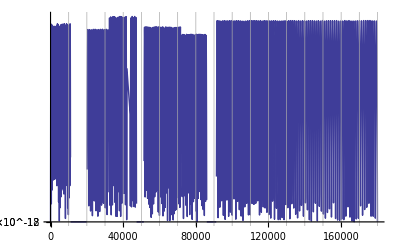

```mathematica
Plot[{
Abs[1/T[h] approximation[xT,yT,tgTout,tgTin][h]-1]},
{h,0,xT//Last},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,180km,10000],10.^Range[-18,30]},
GridLines->{Range[0,180km,10000],Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

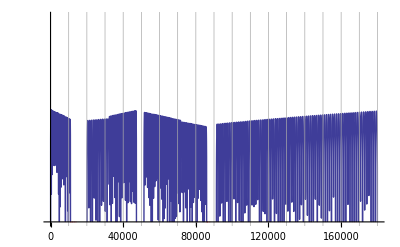

```mathematica
LogPlot[{
Abs[T[h]-approximation[xT,yT,tgTout,tgTin][h]]},
{h,0,xT//Last},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,180km,10000],10.^Range[-18,30]},
GridLines->{Range[0,180km,10000],Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

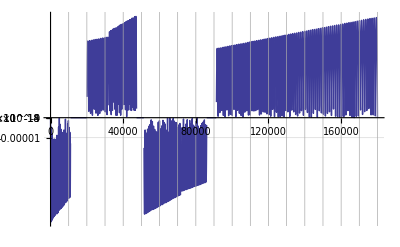

```mathematica
Plot[{
T[h]-approximation[xT,yT,tgTout,tgTin][h]},
{h,0,xT//Last},PlotStyle->Thick,
ImageSize->Full,Ticks->{Range[0,180km,10000],Flatten[{#,-#}&/@(10.^Range[-18,30])]},
GridLines->{Range[0,180km,10000],Flatten[{#,-#}&/@Outer[Times,10.^Range[-18,30],Range[1,9,1]]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

```mathematica
keyFrames[xT/km,yT-Celsius0,tgTin/(1/km),tgTout/(1/km)]
```

key =   0.                   15.                   -12013.137972086231   -6.499538520406088
key =   0.4521741254136301   12.061076771087244    -6.499538886871079    -6.498618366688185
key =   0.9020843085907556   9.13728210848194      -6.498618734972649    -6.497703026148511
key =   1.3497298712981953   6.228614098190974     -6.497703396271569    -6.496792497185025
key =   1.795110138160679    3.335070839205116     -6.496792869166099    -6.495886778205062
key =   2.2382244366578816   0.4566504435295542    -6.495887152063877    -6.494985867625589
key =   2.679072097121345    -2.406648963785017    -6.494986243382183    -6.494089763872719
key =   3.117652452731285    -5.2548292446103915   -6.494090141547442    -6.493198465382328
key =   3.5539648395132764   -8.087892247708396    -6.493198844995862    -6.492311970599505
key =   3.9880085963348195   -10.905839808697465   -6.492312352172857    -6.491430277979252
key =   4.41978306490178     -13.708673750018761   -6.491430661533771    -6.490553385985386
key =   4.849287589754702    -16.496395880901048   -6.4905537715427615   -6.489681293092004
key =   5.276521518264989    -19.26900799732539    -6.489681680674284    -6.488813997781865
key =   5.70148420063095     -22.02651188198834    -6.4888143874114546   -6.487951498548098
key =   6.124174989873708    -24.768909304265037   -6.487951890247773    -6.487093793892608
key =   6.544593241832969    -27.496202020170728   -6.48709418768552     -6.486240882327267
key =   6.96273831516264     -30.20839177232193    -6.486241278236955    -6.485392762373473
key =   7.378609571326308    -32.9054802898965     -6.4853931604238655   -6.484549432561891
key =   7.792206374592554    -35.587469288592644   -6.484549832777321    -6.4837108914330015
key =   8.203528092030119    -38.25436047058719    -6.4837112938382155   -6.482877137536601
key =   8.612574093502909    -40.906155524492675   -6.482877542156765    -6.482048169432417
key =   9.019343751664818    -43.542856125313676   -6.482048576293131    -6.481223985689547
key =   9.42383644195442     -46.16446393440185    -6.481224394816844    -6.480404584886574
key =   9.82605154258943     -48.77098059940994    -6.4804049963069446   -6.479589965611892
key =   10.225988434561039   -51.3624077542448     -6.479590379352287    -6.47878012646334
key =   10.623646501628029   -53.93874701901916    -6.4787805425511795   -6.477975066048612
key =   11.01902513031035    -56.5                 -6.477975484511803    0
key =   20.062982118274434   -56.5                 0                     0.9935768014307329
key =   21.05743029759848    -55.511939346095545   0.9935768269766928    0.9932673093065625
key =   22.05437619410376    -54.52170556524845    0.9932673347845417    0.9929571857150586
key =   23.053821297954343   -53.529299354953196   0.9929572111253496    0.992646431193125
key =   24.055767103357713   -52.53472141427352    0.9926464565360199    0.9923350462784477
key =   25.060215108569764   -51.53797244384202    0.9923350715542352    0.9920230315100956
key =   26.06716681589978    -50.53905314585913    0.9920230567190635    0.9917103874278936
key =   27.07662373171546    -49.53796422409269    0.9917104125703271    0.9913971145728618
key =   28.08858736644792    -48.534706383877165   0.9913971396490445    0.991083213487051
key =   29.103059234596746   -47.52928033211293    0.9910832384972645    0.9907686847135218
key =   30.120040854735016   -46.52168677726564    0.9907687096580456    0.9904535287964386
key =   31.139533749514385   -45.511926429365474   0.9904535536755508    0.9901377462808884
key =   32.16153944567676    -44.5                 0.9901377710948644    2.7716693450916465
key =   32.79413474471147    -42.74665496631073    2.771669457340149     2.771120716311241
key =   33.42924496681564    -40.986687837194694   2.771120828104017     2.7705700741653008
key =   34.06687110702809    -39.220099899118      2.7705701855057323    2.7700174196727723
key =   34.70701416428456    -37.446892443940044   2.7700175305642016    2.7694627538563332
key =   35.34967514142245    -35.66706676890837    2.769462864302066     2.768906077742717
key =   35.99485504518566    -33.880624176653214   2.768906187746022     2.76834739236211
key =   36.64255488622925    -32.08756597518271    2.768347501926218     2.7677866987490574
key =   37.29277567912426    -30.28789347787736    2.767786807877164     2.7672239979413886
key =   37.945518442362385   -28.481608003485405   2.7672241066366525    2.7666592909811345
key =   38.60078419836077    -26.66871087611753    2.766659399246681     2.7660925789138204
key =   39.258573973466675   -24.849203425242223   2.766092686752738     2.7655238627892484
key =   39.91888879796221    -23.02308698568052    2.7655239702045935    2.7649531436603274
key =   40.58172970606906    -21.190362897601716   2.7649532506551213    2.7643804225845763
key =   41.24709773595319    -19.35103250651798    2.7643805291618087    2.763805700622599
key =   41.91499392972952    -17.50509716328017    2.7638058067852267    2.7632289788392024
key =   42.58541933346663    -15.65255822407289    2.7632290845901486    2.7626502583029406
key =   43.25837499719148    -13.793417050409857   2.7626503636450983    2.762069540085885
key =   43.93386197489405    -11.92767500912953    2.7620696450221143    2.7614868252644786
key =   44.61188132453204    -10.055333472390203   2.7614869297976115    2.760902114918052
key =   45.29243410803557    -8.17639381766611     2.7609022190508874    2.760315410130616
key =   45.97552139131184    -6.290857427742367    2.7603155138659243    2.7597267119893543
key =   46.661144244249776   -4.3987256907109895   2.759726815329876     2.759136021585451
key =   47.34930374071258    -2.5                  2.7591361245338986    0
key =   51.41155004684329    -2.5                  0                     -2.7550633482713027
key =   52.08282196911265    -4.349396705166441    -2.755063453732727    -2.7544884897022492
key =   52.75190138805197    -6.192368298726308    -2.7544885954983513   -2.7539156912292486
key =   53.41878735324601    -8.028916057925926    -2.7539157973624215   -2.7533449518312803
key =   54.083478917099214   -9.859041255173565    -2.753345058303939    -2.7527762704916405
key =   54.74597513483757    -11.68274515803813    -2.752776377306227    -2.7522096461970453
key =   55.406275064510346   -13.500029029247116   -2.752209753356026    -2.751645077938029
key =   56.06437776699183    -15.310894126684786   -2.7516451854438975   -2.751082564709314
key =   56.72028230598313    -17.11534170339064    -2.751082672564588    -2.750522105509174
key =   57.37398774801383    -18.91337300755734    -2.7505222137163994   -2.7499636993398973
key =   58.02549316244369    -20.704989282528913   -2.7499638079016453   -2.7494073452076866
key =   58.67479762146432    -22.490191766798887   -2.749407454126557    -2.748853042122083
key =   59.32190020010084    -24.268981694007948   -2.7488531514007013   -2.7483007890970512
key =   59.96679997621348    -26.04136029294233    -2.7483008987380733   -2.747750585150239
key =   60.60949603049918    -27.807328787531617   -2.7477506951563475   -2.7472024293027753
key =   61.24998744649317    -29.566888396846423   -2.7472025396766826   -2.746656320580227
key =   61.888273310570526   -31.320040335096564   -2.7466564313246735   -2.7461122580113915
key =   62.524352711947685   -33.066785811628534   -2.7461123691291482   -2.74557024062929
key =   63.15822474268395    -34.80712603092343    -2.7455703521231576   -2.745030267470435
key =   63.789888497682945   -36.54106219259444    -2.745030379343245    -2.7444923375758465
key =   64.41934307469413    -38.268595491384986   -2.744492449830461    -2.743956449989299
key =   65.04658757431413    -39.98972711716553    -2.7439565626286115   -2.7434226037594733
key =   65.67162109998823    -41.704458254931865   -2.7434227167864105   -2.7428907979381005
key =   66.2944427580117     -43.41279008480211    -2.742890911355618    -2.7423610315810163
key =   66.91505165753111    -45.11472378201432    -2.742361145392106    -2.741833303748039
key =   67.5334469105457     -46.810260516923904   -2.741833417955725    -2.741307613502574
key =   68.14962763190871    -48.499401455000935   -2.7413077281099136   -2.74078395991184
key =   68.76359293932852    -50.18214775682725    -2.740784074921926    -2.740262342046984
key =   69.37534195336997    -51.85850057809387    -2.7402624574629417   -2.7397427589829437
key =   69.98487379745558    -53.52846106959811    -2.7397428748079364   -2.7392252097984735
key =   70.59218759786667    -55.1920303772406     -2.7392253260356996   -2.7387096935760433
key =   71.19728248374456    -56.84920964202229    -2.7387098102287366   -2.7381962094020835
key =   71.80015758707647    -58.5                 -2.7381963264735156   -1.955459829148327
key =   72.49731970661351    -59.8632725443629     -1.9554599014498824   -1.9550373671359902
key =   73.19237721278938    -61.2221359664467     -1.955037439648716    -1.9546163189471575
key =   73.88532916052561    -62.576591176937086   -1.9546163916724624   -1.954196683857998
key =   74.57617460733861    -63.926639083353706   -1.9541967567973029   -1.95377846114683
key =   75.2649126133417     -65.27228059004932    -1.9537785343015706   -1.9533616500943058
key =   75.95154224124693    -66.6135165982088     -1.9533617234659306   -1.9529462499840904
key =   76.63606255636705    -67.95034800584884    -1.9529463235740632   -1.9525322601022306
key =   77.31847262661748    -69.28277570781702    -1.9525323339120284   -1.9521196797369653
key =   77.99877152251806    -70.61080059579086    -1.9521197537680794   -1.9517085081796637
key =   78.67695831719504    -71.93442355827736    -1.9517085824336005   -1.9512987447235983
key =   79.35303208638285    -73.25364548061182    -1.9512988192018783   -1.950890388665139
key =   80.02699190842597    -74.56846724495733    -1.9508904633692987   -1.9504834393028967
key =   80.69883686428072    -75.87888973030371    -1.9504835142344867   -1.9500778959377831
key =   81.36856603751708    -77.18491381246656    -1.95007797109837     -1.9496737578763577
key =   82.03617851432051    -78.48654036408675    -1.9496738332626624   -1.9492710244171634
key =   82.70167338349361    -79.78377025462885    -1.9492711000401768   -1.948869694876361
key =   83.36504973645799    -81.07660435038093    -1.9488697707334928   -1.9484697685628305
key =   84.0263066672559     -82.36504351445294    -1.9484698446553819   -1.9480712447904558
key =   84.68544327255199    -83.64908860677616    -1.948071321120073    -1.9476741228753822
key =   85.342458651635      -84.92874048410187    -1.947674199443728    -1.947278402136563
key =   85.99735190641914    -86.20400000000001    -1.9472784789453172   0
key =   91.28960171845002    -86.20400000000001    0                     0.9718021776719401
key =   92.24973695484589    -85.27093847384779    0.9718022038395262    0.9715131008080296
key =   93.21247978175415    -84.33562119223618    0.9715131269008468    0.9712233691834314
key =   94.17783169482969    -83.39804884221189    0.9712233952018344    0.9709329833231084
key =   95.14579419406051    -82.4582221125313     0.9709330092674485    0.9706419437532052
key =   96.11636878377311    -81.51614169365956    0.9706419696238318    0.9703502510010168
key =   97.08955697263775    -80.5718082777698     0.9703502767982765    0.9700579055950165
key =   98.06536027367368    -79.62522255874234    0.9700579313192531    0.9697649080647676
key =   99.04378020425452    -78.67638523216394    0.9697649337163228    0.9694712589410539
key =   100.02481828611347   -77.72529699532697    0.9694712845202663    0.9691769587557034
key =   101.00847604534881   -76.77195854722868    0.9691769842629098    0.9688820080418635
key =   101.9947550124291    -75.81637058857027    0.9688820334773977    0.9685864073335658
key =   102.98365672219855   -74.85853382175634    0.9685864326977593    0.9682901571662595
key =   103.97518271388249   -73.89844895089388    0.9682901824594415    0.9679932580763205
key =   104.96933453109267   -72.93611668179165    0.967993283298818     0.9676957106013957
key =   105.9661137218327    -71.97153772195927    0.967695735753533     0.9673975152802152
key =   106.96552183850339   -71.00471278060655    0.9673975403623144    0.9670986726526218
key =   107.96756043790835   -70.03564256864269    0.9670986976650026    0.9667991832596814
key =   108.97223108125921   -69.06432779867538    0.9667992082026612    0.9664990476434572
key =   109.97953533418125   -68.09076918501026    0.9664990725173512    0.9661982663472779
key =   110.98947476671879   -67.11496744364993    0.9661982911523991    0.9658968399155521
key =   112.00205095334066   -66.13692329229326    0.9658968646522113    0.9655947688937826
key =   113.0172654729458    -65.15663745033464    0.9655947935622882    0.9652920538285802
key =   114.03511990886862   -64.17411063886323    0.9652920784292385    0.9649886952678585
key =   115.0556158488847    -63.18934358066201    0.9649887198009734    0.9646846937603855
key =   116.07875488521617   -62.20233700020731    0.9646847182262595    0.9643800498562735
key =   117.10453861453738   -61.213091623667765   0.9643800742552061    0.964074764106724
key =   118.13296863798041   -60.22160817890364    0.964074788439013     0.9637688370638785
key =   119.16404656114068   -59.22788739546618    0.9637688613298198    0.9634622692812039
key =   120.19777399408255   -58.231930004596734   0.9634622934810909    0.9631550613132569
key =   121.23415255134495   -57.23373673922589    0.9631550854473813    0.9628472137155605
key =   122.27318385194695   -56.23330833397296    0.9628472377842119    0.9625387270448917
key =   123.31486951939347   -55.230645525145036   0.9625387510483576    0.9622296018591573
key =   124.35921118168092   -54.225749050736226   0.9622296257977231    0.9619198387172846
key =   125.40621047130286   -53.21861965042697    0.961919862591234     0.961609438179303
key =   126.45586902525568   -52.2092580655833     0.9616094619889176    0.9612984008064254
key =   127.50818848504437   -51.19766503925598    0.961298424551985     0.960986727160993
key =   128.56317049668817   -50.18384131617975    0.9609867508427753    0.9606744178063393
key =   129.6208167107263    -49.16778764277268    0.9606744414246202    0.9603614733069672
key =   130.68112878222377   -48.14950476713534    0.9603614968620205    0.9600478942285334
key =   131.7441083707771    -47.128993439049964   0.9600479177206316    0.9597336811376346
key =   132.80975714052016   -46.1062544099799     0.9597337045670478    0.9594188346021678
key =   133.8780767601298    -45.081288433068636   0.9594188579691644    0.9591033551909975
key =   134.94906890283193   -44.054096263139144   0.9591033784958443    0.9587872434741269
key =   136.0227352464071    -43.02467865669314    0.9587872667170885    0.9584705000226335
key =   137.09907747319647   -41.99303637191031    0.958470523203973     0.9581531254087333
key =   138.1780972701076    -40.95917016864752    0.9581531485287121    0.9578351202056639
key =   139.2597963286204    -39.92308080843813    0.9578351432645414    0.9575164849878542
key =   140.344176344793     -38.88476905449113    0.9575165079858885    0.9571972203306744
key =   141.4312390192676    -37.84423567169057    0.9571972432681216    0.9568773268107137
key =   142.52098605727642   -36.80148142659462    0.956877349687828     0.9565568050056847
key =   143.61341916864765   -35.75650708743484    0.9565568278227189    0.9562356554941275
key =   144.7085400678114    -34.70931342411566    0.9562356782513326    0.9559138788559939
key =   145.8063504738057    -33.659901208213284   0.9559139015536193    0.9555914756721141
key =   146.90685211028241   -32.608271212975154   0.9555914983104076    0.9552684465244438
key =   148.01004670551322   -31.55442421331918    0.9552684691036515    0.9549447919960264
key =   149.11593599239575   -30.49836098583293    0.9549448145163927    0.9546205126709536
key =   150.22452170845955   -29.440082308772958   0.9546205351327215    0.954295609134481
key =   151.33580559587207   -28.379588962063934   0.9542956315378918    0.953970081972786
key =   152.44978940144492   -27.31688172729804    0.9539701043180794    0.9536439317733371
key =   153.5664748766397    -26.251961387734042   0.9536439540607513    0.9533171591244236
key =   154.68586377757424   -25.184828728296765   0.9533171813541952    0.9529897646155253
key =   155.80795786502875   -24.1154845355762     0.9529897867878897    0.9526617488373238
key =   156.93275890445187   -23.04392959782666    0.9526617709525144    0.9523331123812601
key =   158.06026866596684   -21.97016470496635    0.9523331344395091    0.9520038558401811
key =   159.19048892437763   -20.894190648576227   0.9520038778417189    0.9516739798077459
key =   160.32342145917525   -19.816008221899494   0.9516740017528018    0.9513434848786638
key =   161.45906805454374   -18.735618219841      0.9513435067674655    0.9510123716489636
key =   162.59743049936657   -17.65302143896602    0.9510123934817372    0.9506806407155233
key =   163.73851058723284   -16.568218677499885   0.9506806624924937    0.9503482926762883
key =   164.88231011644336   -15.481210735327181   0.9503483143976789    0.9500153281303091
key =   166.02883089001713   -14.391998413990905   0.9500153497963416    0.9496817476777271
key =   167.17807471569756   -13.30058251669169    0.9496817692886221    0.9493475519196137
key =   168.33004340595866   -12.206963848287273   0.9493475734755906    0.9490127414581113
key =   169.48473877801146   -11.111143215291634   0.9490127629593875    0.9486773168966633
key =   170.64216265381037   -10.013121425873976   0.9486773383434555    0.9483412788394129
key =   171.8023168600594    -8.912899289858444    0.948341300231936     0.9480046278917355
key =   172.96520322821866   -7.810477618723041    0.9480046492302032    0.9476673646600242
key =   174.13082359451064   -6.705857225599061    0.9476673859446488    0.9473294897516861
key =   175.29917979992672   -5.599038925270236    0.9473295109826788    0.9469910037751724
key =   176.47027369023348   -4.49002353417211     0.946991024952743     0.9466519073400709
key =   177.64410711597915   -3.3788118703910754   0.9466519284644277    0.9463122010568948
key =   178.8206819325002    -2.265404753663802    0.946312222128245     0.9459718855372189
key =   179.9999999999276    -1.1498030053764978   0.9459719065557683    -4.603771494730113e-8

## Inverse square power curve

## Constants.

```mathematica
AstronomicalUnit=149597870700.;
SednaAphelion=1.4*^14;
SolarRadius=696342000.;
```

```mathematica
f[d_]:=(AstronomicalUnit/d)^2
```

## Interpolation.

```mathematica
xP=steps[f,SolarRadius,SednaAphelion,400];
polyP=bestContinuousInterpolatingPiecewiseCubic[f,xP,d,-1*^6];
dPolyP=D[polyP,d];
tgPin=Prepend[Table[dPolyP⟦j-1⟧/.d->xP⟦j⟧,{j,2,Length[xP]}],f'[xP⟦1⟧]];
tgPout=Append[Table[dPolyP⟦j⟧/.d->xP⟦j⟧,{j,1,Length[xP]-1}],f'[xP⟦-1⟧]];
yP=f/@xP;
```

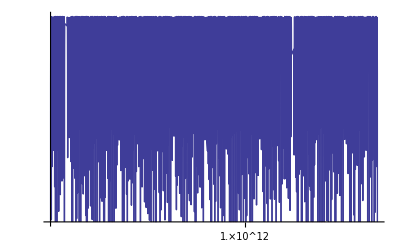

```mathematica
LogLogPlot[{
Abs[1/f[h] approximation[xP,yP,tgPout,tgPin][h]-1]},
{h,xP//First,xP//Last},PlotStyle->Thick,
ImageSize->Full,Ticks->{10.^Range[-18,30],Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]]},
GridLines->{Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]],Flatten@Outer[Times,10.^Range[-18,30],Range[1,9,1]]},
GridLinesStyle->Lighter@Gray,ClippingStyle->Red
]
```

## Output.

```mathematica
keyFrames[xP,yP,tgPin,tgPout]
```

key =   6.96342e8               46153.606505845986        -0.0001325601687269933     -0.00012664155800798363
key =   7.179279380019401e8     43419.92968612424         -0.00012664155801628288    -0.00011555838241283948
key =   7.401830194986337e8     40848.16846781357         -0.0001155583824204124     -0.00010544516315118556
key =   7.631279873003552e8     38428.73259438066         -0.00010544516315809574    -0.0000962170134249366
key =   7.867842272247182e8     36152.59983991784         -0.00009621701343124202    -0.0000877964753977453
key =   8.1117378802929e8       34011.28236470514         -0.0000877964754034989     -0.000080112870041228
key =   8.363194019620976e8     31996.795063531205        -0.00008011287004647805    -0.00007310170388010172
key =   8.622445059491808e8     30101.62578874261         -0.00007310170388489232    -0.00006670412765669282
key =   8.88973263438938e8      28318.70733698086         -0.00006670412766106416    -0.00006086644237100281
key =   9.16530586923627e8      26641.391095144318        -0.00006086644237499159    -0.00005553964855023401
key =   9.449421611590102e8     25063.42224729897         -0.00005553964855387371    -0.00005067903496447889
key =   9.742344671037868e8     23578.916450083296        -0.00005067903496780005    -0.00004624380333641886
key =   1.0044348066011251e9    22182.337889628143        -0.000046243803339449376   -0.000042196725894964126
key =   1.0355713278252975e9    20868.478638164645        -0.00004219672589772941    -0.00003850383289846045
key =   1.0676730515171381e9    19632.439233339726        -0.00003850383290098374    -0.00003513412750465259
key =   1.1007698980327744e9    18469.610407818178        -0.00003513412750695505    -0.000032059325594116426
key =   1.134892715230843e9     17375.65590103984         -0.00003205932559621738    -0.00002925361836332675
key =   1.1700733072241833e9    16346.496289036006        -0.000029253618365243836   -0.00002669345569465797
key =   1.2063444640228057e9    15378.293772005294        -0.000026693455696407282   -0.000024357348484997614
key =   1.2437399920957642e9    14467.437862920977        -0.00002435734848659383    -0.000022225688273787032
key =   1.2822947458804169e9    13610.53192380174         -0.000022225688275243556   -0.000020280582656515828
key =   1.322044660268445e9     12804.380499438686        -0.00002028058265784488    -0.000018505705102183966
key =   1.3630267840989058e9    12045.977401345384        -0.000018505705103396707   -0.000016886157914154826
key =   1.4052793146895392e9    11332.4944974952          -0.00001688615791526143    -0.00001540834718414077
key =   1.448841633438512e9     10661.271166042156        -0.000015408347185150528   -0.00001405986868972743
key =   1.4937543425297825e9    10029.804373697643        -0.000014059868690648818   -0.000012829403777703093
key =   1.5400593027762947e9    9435.739341764589         -0.000012829403778543846   -0.00001170662435927304
key =   1.5877996726362777e9    8876.860765022137         -0.000011706624360040212   -0.000010682106219721772
key =   1.6370199484390118e9    8351.084550715575         -0.000010682106220421804   -9.747249914876786e-6
key =   1.6877660058575559e9    7856.450046845637         -9.747249915515555e-6      -8.894208590404826e-6
key =   1.740085142667088e9     7391.112730776018         -8.894208590987692e-6      -8.115822118082095e-6
key =   1.7940261228287168e9    6953.337330894462         -8.115822118613952e-6      -7.405556996201756e-6
key =   1.8496392219398456e9    6541.491355677674         -7.405556996687067e-6      -6.757451509663305e-6
key =   1.9069762740934572e9    6154.039006029524         -6.757451510106143e-6      -6.166065689437183e-6
key =   1.9660907201899905e9    5789.535448191298         -6.166065689841266e-6      -5.6264356513819186e-6
key =   2.027037657746839e9     5446.621425867319         -5.626435651750637e-6      -5.134031931150483e-6
key =   2.089873892251897e9     5124.018191474198         -5.134031931486933e-6      -4.684721465462511e-6
key =   2.1546579901090174e9    4820.522737612075         -4.6847214657695155e-6     -4.274732900628311e-6
key =   2.2214503332247252e9    4535.003310975662         -4.274732900908448e-6      -3.900624937134892e-6
key =   2.290313175287071e9     4266.395191976224         -3.900624937390513e-6      -3.5592574445907925e-6
key =   2.3613106997890735e9    4013.6967243364224        -3.5592574448240425e-6     -3.247765104578408e-6
key =   2.4345090798508315e9    3775.9655798521494        -3.247765104791245e-6      -2.963533360180925e-6
key =   2.5099765398960686e9    3552.3152443924164        -2.963533360375135e-6      -2.704176470313229e-6
key =   2.587783419240587e9     3341.911712033364         -2.704176470490443e-6      -2.4675174846519337e-6
key =   2.668002237651908e9     3143.970374998628         -2.4675174848136387e-6     -2.2515699710816864e-6
key =   2.7507077629411936e9    2957.7530978084474        -2.251569971229239e-6      -2.0545213422841924e-6
key =   2.8359770806504574e9    2782.565464726838         -2.054521342418832e-6      -1.8747176415189963e-6
key =   2.92388966590001e9      2617.7541902423936        -1.8747176416418527e-6     -1.7106496598935808e-6
key =   3.0145274574631085e9    2462.7046829262385        -1.7106496600056852e-6     -1.560940268595834e-6
key =   3.1079749341368475e9    2316.838753582604         -1.5609402686981276e-6     -1.4243328597601923e-6
key =   3.2043191934804773e9    2179.6124591455805        -1.4243328598535337e-6     -1.299680798944114e-6
key =   3.3036500329945326e9    2050.5140742818044        -1.2996807990292863e-6     -1.1859378006826203e-6
key =   3.406060033816438e9     1929.0621831350672        -1.1859378007603388e-6     -1.0821491463369785e-6
key =   3.511644647010598e9     1814.8038840968288        -1.0821491464078952e-6     -9.874436705228648e-7
key =   3.6205022825333953e9    1707.3131009081283        -9.874436705875752e-7      -9.010264488551664e-7
key =   3.732734400956022e9     1606.188993794882         -9.010264489142137e-7      -8.221721256329214e-7
key =   3.8484456080306287e9    1511.054464711589         -8.22172125686801e-7       -7.502188254591534e-7
key =   3.9677437521879363e9    1421.5547511194147        -7.502188255083177e-7      -6.845625976921007e-7
key =   4.090740025057179e9     1337.3561030547564        -6.845625977369623e-7      -6.246523470963938e-7
key =   4.21754906510207e9      1258.144538555            -6.246523471373293e-7      -5.699852081438562e-7
key =   4.348289064469383e9     1183.624672800378         -5.699852081812092e-7      -5.201023241375351e-7
key =   4.483081879149742e9     1113.518616605716         -5.201023241716191e-7      -4.7458499573025015e-7
key =   4.622053142553282e9     1047.5649401544927        -4.745849957613513e-7      -4.330511665099357e-7
key =   4.765332382606054e9     985.5176981108873         -4.330511665383149e-7      -3.9515221615266666e-7
key =   4.913053142476308e9     927.1455124744297         -3.9515221617856225e-7     -3.605700342266211e-7
key =   5.065353105043165e9     872.2307097571305         -3.6057003425025045e-7     -3.290143500851736e-7
key =   5.222374221223716e9     820.5685092655937         -3.2901435010673505e-7     -3.002202964374269e-7
key =   5.384262842278119e9     771.9662594611533         -3.002202964571013e-7      -2.739461861455094e-7
key =   5.551169856216048e9     726.2427195503783         -2.739461861634619e-7      -2.4997148358792487e-7
key =   5.723250828431595e9     683.2273836269532         -2.4997148360430627e-7     -2.2809495356127235e-7
key =   5.90066614669773e9      642.7598448446142         -2.2809495357622015e-7     -2.0813297218288405e-7
key =   6.083581170655446e9     604.6891972501058         -2.081329721965237e-7      -1.899179856166503e-7
key =   6.27216638593693e9      568.8734730455548         -1.8991798562909626e-7     -1.7329710368520402e-7
key =   6.466597563066397e9     535.1791131817755         -1.7329710369656074e-7     -1.5813081656362662e-7
key =   6.667055921286709e9     503.4804693083232         -1.5813081657398946e-7     -1.442918237831708e-7
key =   6.873728297464453e9     473.65933522302805        -1.4429182379262672e-7     -1.3166396571598256e-7
key =   7.086807320230923e9     445.6045060737612         -1.3166396572461094e-7     -1.201412485721269e-7
key =   7.3064915895213e9       419.21136366866864        -1.2014124858000016e-7     -1.0962695472507239e-7
key =   7.532985861679383e9     394.38148634846783        -1.096269547322566e-7      -1.0003283089802491e-7
key =   7.766501240300381e9     371.02228196599657        -1.000328309045804e-7      -9.127834739702306e-8
key =   8.0072553729896555e9    349.0466426043739         -9.127834740300484e-8      -8.329002217307058e-8
key =   8.2554726542207985e9    328.37261974619463        -8.329002217852883e-8      -7.600080403972065e-8
key =   8.51138443448211e9      308.9231186824419         -7.600080404470125e-8      -6.934950986904024e-8
key =   8.775229235906424e9     290.62561102155365        -6.934950987358496e-8      -6.328031104200704e-8
key =   9.047252974585245e9     273.41186422656693        -6.3280311046154e-8        -5.774226484275209e-8
key =   9.327709189774427e9     257.2176871717705         -5.774226484653612e-8      -5.2688886863359586e-8
key =   9.616859280204988e9     241.98269077003002        -5.268888686681246e-8      -4.807776083013073e-8
key =   9.914972747719353e9     227.6500627781495         -4.807776083328142e-8      -4.387018257633127e-8
key =   1.0222327448460075e10   214.16635594050504        -4.3870182579206225e-8     -4.003083517305748e-8
key =   1.0539209851845179e10   201.48128868092533        -4.003083517568083e-8      -3.6527492491382135e-8
key =   1.0865915307571484e10   189.54755759958618        -3.6527492493775896e-8     -3.3330748707586014e-8
key =   1.120274832089478e10    178.32066107570935        -3.333074870977029e-8      -3.041377148103851e-8
key =   1.1550022836443422e10   167.75873331826793        -3.041377148303162e-8      -2.7752076732986797e-8
key =   1.1908062530829887e10   157.8223882458641         -2.7752076734805486e-8     -2.532332313582883e-8
key =   1.2277201114332994e10   148.47457261359713        -2.5323323137488348e-8     -2.310712458788232e-8
key =   1.2657782641931993e10   139.68042783922354        -2.3107124589396606e-8     -2.1084879099634386e-8
key =   1.305016183398242e10    131.40716001334872        -2.1084879101016148e-8     -1.923961265519521e-8
key =   1.3454704406832584e10   123.62391760891265        -1.9239612656456047e-8     -1.755583673839355e-8
key =   1.387178741368887e10    116.30167643393818        -1.755583673954404e-8      -1.6019418327629677e-8
key =   1.4301799596047512e10   109.41313139852551        -1.6019418328679482e-8     -1.4617461268273257e-8
key =   1.4745141746020447e10   102.93259469248432        -1.4617461269231188e-8     -1.3338198026887266e-8
key =   1.5202227079892906e10   96.8358999939017          -1.3338198027761363e-8     -1.2170890918698573e-8
key =   1.567348162326094e10    91.10031235143458         -1.217089091949617e-8      -1.1105741979258372e-8
key =   1.6159344608107838e10   85.70444340427042         -1.1105741979986169e-8     -1.0133810723779567e-8
key =   1.666026888218954e10    80.62817162360835         -1.013381072444367e-8      -9.246939103860699e-9
key =   1.7176721331110611e10   75.85256727823423         -9.246939104466681e-9      -8.437683031701256e-9
key =   1.770918331348415e10    71.3598218443833          -8.437683032254205e-9      -7.699249897053508e-9
key =   1.8258151109581272e10   67.13318159665413         -7.699249897558065e-9      -7.0254415524455e-9
key =   1.882413638388826e10    63.15688513233128         -7.0254415529059006e-9     -6.410602288116019e-9
key =   1.9407666662002575e10   59.416104596140364        -6.410602288536126e-9      -5.849571359979945e-9
key =   2.0009285822312176e10   55.89689038625931         -5.849571360363287e-9      -5.337639672161502e-9
key =   2.0629554602916435e10   52.58611913539098         -5.337639672511295e-9      -4.870510250503243e-9
key =   2.126905112426111e10    49.47144477291541         -4.870510250822424e-9      -4.444262175279221e-9
key =   2.1928371427974506e10   46.54125248562941         -4.444262175570468e-9      -4.055317670376897e-9
key =   2.260813003240706e10    43.784615405390255        -4.055317670642656e-9      -3.7004120727053814e-9
key =   2.3308960505392086e10   41.19125386214907         -3.700412072947882e-9      -3.3765664297640795e-9
key =   2.4031516054761597e10   38.751497050425854        -3.3765664299853565e-9     -3.0810624953653394e-9
key =   2.477647013716753e10    36.45624696627813         -3.081062495567252e-9      -2.811419913634069e-9
key =   2.5544517085775856e10   34.29694448028189         -2.8114199138183112e-9     -2.565375399774525e-9
key =   2.633637275741861e10    32.26553742000904         -2.5653753999426427e-9     -2.3408637428556167e-9
key =   2.715277519980701e10    30.35445054297873         -2.3408637430090215e-9     -2.1360004711582095e-9
key =   2.799448533942756e10    28.556557288109886        -2.136000471298189e-9      -1.949066034583564e-9
key =   2.8862287690762257e10   26.86515320033456         -1.949066034711293e-9      -1.7784913713560628e-9
key =   2.975699108749397e10    25.27393092927052         -1.7784913714726133e-9     -1.6228447378714562e-9
key =   3.0679429436378468e10   23.77695670872193         -1.6228447379778066e-9     -1.4808196911458744e-9
key =   3.163046249448578e10    22.36864822929839         -1.4808196912429176e-9     -1.3512241229937434e-9
key =   3.2610976670535282e10   21.04375382163823         -1.3512241230822937e-9     -1.2329702538918616e-9
key =   3.362188585107141e10    19.797332872608898        -1.2329702539726623e-9     -1.1250655025415246e-9
key =   3.4664132252250046e10   18.624737401455167        -1.1250655026152539e-9     -1.0266041544908207e-9
key =   3.573868729802945e10    17.521594727191708        -1.0266041545580973e-9     -9.367597598868946e-10
key =   3.684655252558428e10    16.48379116260536         -9.367597599482834e-10     -8.547781965470258e-10
key =   3.7988760518786606e10   15.507456674061313        -8.547781966030423e-10     -7.799713401228968e-10
key =   3.916637587062389e10    14.588950449908472        -7.79971340174011e-10      -7.117112882273265e-10
key =   4.038049617545108e10    13.724847323667783        -7.117112882739672e-10     -6.49425090042899e-10
key =   4.1632253052001495e10   12.911925001374762        -6.494250900854579e-10     -5.925899371748057e-10
key =   4.292281319811014e10    12.14715204544611         -5.925899372136401e-10     -5.407287753813821e-10
key =   4.42533794781324e10     11.427676570261616        -5.407287754168179e-10     -4.934063003489622e-10
key =   4.5625192044071686e10   10.750815607306441        -4.934063003812968e-10     -4.5022530390092256e-10
key =   4.703952949146096e10    10.114045100215648        -4.5022530393042727e-10    -4.1082333997217336e-10
key =   4.84977100510755e10     9.514990492412082         -4.1082333999909597e-10    -3.7486968236470903e-10
key =   5.000109281758762e10    8.951417872238075         -3.748696823892755e-10     -3.420625487484129e-10
key =   5.155107901630851e10    8.421225642560842         -3.420625487708294e-10     -3.1212656760656583e-10
key =   5.314911330919785e10    7.922436683786863         -3.1212656762702056e-10    -2.848104668643825e-10
key =   5.4796685141358536e10   7.453190981060728         -2.848104668830471e-10     -2.5988496479977915e-10
key =   5.649533012927137e10    7.011738688154773         -2.598849648168103e-10     -2.3714084553339926e-10
key =   5.824663149206378e10    6.596433602184363         -2.3714084554893986e-10    -2.1638720294427634e-10
key =   6.005222152714646e10    6.205727024815571         -2.163872029584569e-10     -1.9744983827112214e-10
key =   6.191378313159335e10    5.8381619870733905        -1.9744983828406168e-10    -1.801697979493381e-10
key =   6.383305137068297e10    5.492367816214356         -1.8016979796114524e-10    -1.644020394108006e-10
key =   6.581181509506297e10    5.167055024403187         -1.6440203942157442e-10    -1.5001421364767565e-10
key =   6.785191860804535e10    4.861010500132942         -1.500142136575066e-10     -1.3688555432148688e-10
key =   6.995526338458612e10    4.573092984457232         -1.3688555433045745e-10    -1.2490586409303872e-10
key =   7.212380984355179e10    4.30222881516508          -1.2490586410122421e-10    -1.1397458966479021e-10
key =   7.435957917492435e10    4.047407923028166         -1.1397458967225933e-10    -1.0399997777190928e-10
key =   7.666465522364792e10    3.807680065190259         -1.0399997777872474e-10    -9.489830503771575e-11
key =   7.904118643187286e10    3.5821512816528616        -9.489830504393476e-11     -8.659317522915631e-11
key =   8.149138784140755e10    3.3699805616431346        -8.659317523483106e-11     -7.901487801375672e-11
key =   8.401754315824422e10    3.1703767074327422        -7.901487801893484e-11     -7.20998038356568e-11
key =   8.662200688108327e10    2.9825953839126216        -7.209980384038173e-11     -6.578990999942026e-11
key =   8.930720649583966e10    2.8059363429213553        -6.578991000373171e-11     -6.003223348010332e-11
key =   9.207564473817699e10    2.6397408119765022        -6.003223348403743e-11     -5.477844637029305e-11
key =   9.492990192617793e10    2.4833890376712895        -5.477844637388286e-11     -4.9984450232683504e-11
key =   9.787263836532527e10    2.3362979745758583        -4.998445023595915e-11     -4.56100059533369e-11
key =   1.00906596828035e11     2.197919111024818         -4.561000595632588e-11     -4.161839598874326e-11
key =   1.0403460511005264e11   2.0677364236833435        -4.161839599147065e-11     -3.797611617169901e-11
key =   1.072595786660954e11    1.945264453264271         -3.797611617418772e-11     -3.4652594489140824e-11
key =   1.1058452332719662e11   1.830046494220406         -3.4652594491411726e-11    -3.161993447143749e-11
key =   1.1401253810228554e11   1.721652891661315         -3.161993447350965e-11     -2.885268103926002e-11
key =   1.1754681806661308e11   1.6196794391436817        -2.8852681041150832e-11    -2.6327606842616054e-11
key =   1.2119065733971631e11   1.5237458713604968        -2.632760684434139e-11     -2.4023517298658985e-11
key =   1.249474521556968e11    1.4334944461082297        -2.4023517300233326e-11    -2.192107269183214e-11
key =   1.288207040286748e11    1.3485886102440368        -2.1921072693268704e-11    -2.0002625843111674e-11
key =   1.3281402301636943e11   1.2687117446582905        -2.0002625844422513e-11    -1.82520739858043e-11
key =   1.369311310848467e11    1.1935659835823542        -1.825207398700042e-11     -1.6654723604601226e-11
key =   1.411758655775716e11    1.1228711038287167        -1.6654723605692668e-11    -1.5197167103387304e-11
key =   1.455521827919974e11    1.0563634798214114        -1.5197167104383226e-11    -1.3867170266606799e-11
key =   1.5006416166702594e11   0.993795100519945         -1.386717026751556e-11     -1.2653569569568053e-11
key =   1.5471600758477545e11   0.9349326445708028        -1.2653569570397284e-11    -1.154617847575314e-11
key =   1.595120562901999e11    0.8795566102376976        -1.1546178476509798e-11    -1.0535701934619822e-11
key =   1.6445677793221234e11   0.8274604968660314        -1.0535701935310263e-11    -9.613658362223721e-12
key =   1.695547812300797e11    0.7784500348291897        -9.613658362853736e-12     -8.77230844979194e-12
key =   1.7481081776897156e11   0.7323424610850967        -8.77230845036682e-12      -8.004590202692665e-12
key =   1.8022978642866675e11   0.6889658376415373        -8.004590203217233e-12     -7.30405966454171e-12
key =   1.8581673794954602e11   0.6481584103887551        -7.30405966502037e-12      -6.664836828903365e-12
key =   1.9157687964012573e11   0.6097680059083814        -6.664836829340134e-12     -6.081556284589017e-12
key =   1.975155802305208e11    0.5736514640093522        -6.081556284987562e-12     -5.5493221802865e-12
key =   2.0363837487636044e11   0.5396741038747076        -5.5493221806501655e-12    -5.063667130510011e-12
key =   2.099509703178202e11    0.5077092218285012        -5.0636671308418495e-12    -4.6205147179404965e-12
key =   2.164592501985794e11    0.4776376188499618        -4.620514718243294e-12     -4.216145277415703e-12
key =   2.2316928054966116e11   0.44934715607297715       -4.216145277692002e-12     -3.847164674371544e-12
key =   2.30087315443266e11     0.42273233661333226       -3.847164674623662e-12     -3.5104758156731814e-12
key =   2.3721980282186902e11   0.39769391216430666       -3.510475815903235e-12     -3.2032526537064037e-12
key =   2.4457339050801364e11   0.3741385128936058        -3.203252653916323e-12     -2.922916465530297e-12
key =   2.521549324004031e11    0.3519782992614846        -2.9229164657218457e-12    -2.6671142079857122e-12
key =   2.599714948620649e11    0.3311306344616747        -2.667114208160497e-12     -2.433698767080104e-12
key =   2.6803036330654224e11   0.3115177762636272        -2.4336987672395924e-12    -2.220710935869614e-12
key =   2.763390489882511e11    0.29306658710693          -2.2207109360151444e-12    -2.0263629695666047e-12
key =   2.8490529600333203e11   0.2757082613668234        -2.026362969699399e-12     -1.849023579839689e-12
key =   2.9373708850752155e11   0.2593780687737742        -1.8490235799608616e-12    -1.6872042423546387e-12
key =   3.028426581577706e11    0.24401511303029952       -1.687204242465207e-12     -1.5395467026257897e-12
key =   3.122304917845465e11    0.22956210472490918       -1.5395467027266813e-12    -1.40481157530644e-12
key =   3.2190933930196826e11   0.21596514769634997       -1.404811575398502e-12     -1.2818679412251995e-12
key =   3.318882218631491e11    0.2031735380514891        -1.2818679413092046e-12    -1.1696838548490042e-12
key =   3.421764402683467e11    0.1911395750873628        -1.1696838549256577e-12    -1.0673176824960157e-12
key =   3.527835836337578e11    0.1798183834123069        -1.0673176825659608e-12    -9.739101985944125e-13
key =   3.6371953832903766e11   0.16916774560284778       -9.73910198658236e-13      -8.88677373645721e-13
key =   3.749944971918736e11    0.15914794477232086       -8.886773737039589e-13     -8.109037933576033e-13
key =   3.8661896902820184e11   0.14972161646414536       -8.109037934107446e-13     -7.399366537083576e-13
key =   3.9860378840692206e11   0.1408536093174566        -7.39936653756848e-13      -6.751802815401026e-13
key =   4.1096012575823834e11   0.1325108539855087        -6.751802815843494e-13     -6.16091134688205e-13
key =   4.236994977850396e11    0.1246622398180365        -6.160911347285794e-13     -5.621732396799099e-13
key =   4.368337781970226e11    0.11727849884771832       -5.62173239716751e-13      -5.129740287078662e-13
key =   4.503752087775623e11    0.1103320966481164        -5.129740287414831e-13     -4.680805409354028e-13
key =   4.643364107936454e11    0.10379712965609914       -4.680805409660777e-13     -4.2711595624883323e-13
key =   4.787303967594999e11    0.09764922857585331       -4.271159562768236e-13     -3.8973643236224887e-13
key =   4.9357058256488684e11   0.09186546750427362       -3.8973643238778953e-13    -3.5562821872653784e-13
key =   5.088707999793572e11    0.08642427843885304       -3.556282187498434e-13     -3.2450502301786114e-13
key =   5.246453095441286e11    0.08130537084926857       -3.2450502303912706e-13    -2.961056081007902e-13
key =   5.409088138635984e11    0.07648965601273953       -2.9610560812019496e-13    -2.701915992958686e-13
key =   5.576764713088805e11    0.0719591758310005        -2.7019159931357514e-13    -2.4654548354656424e-13
key =   5.749639101461389e11    0.06769703586344306       -2.4654548356272117e-13    -2.2496878369134197e-13
key =   5.927872431028866e11    0.06368734232670233       -2.2496878370608493e-13    -2.0528039251630705e-13
key =   6.111630823858251e11    0.059915142825756766      -2.0528039252975977e-13    -1.8731505260509962e-13
key =   6.301085551642228e11    0.05636637059552289       -1.8731505261737503e-13    -1.7092196922638012e-13
key =   6.496413195332642e11    0.05302779204501873       -1.7092196923758124e-13    -1.5596354461599822e-13
key =   6.697795809722462e11    0.04988695740848536       -1.55963544626219e-13      -1.4231422302986285e-13
key =   6.905421093129644e11    0.046932154319440776      -1.4231422303918915e-13    -1.298594368732764e-13
key =   7.119482562341017e11    0.0441523641345414        -1.2985943688178654e-13    -1.1849464506092238e-13
key =   7.340179732979276e11    0.04153722084438006       -1.1849464506868772e-13    -1.081244555358398e-13
key =   7.567718305461172e11    0.039076972417996264      -1.0812445554292555e-13    -9.86618245821252e-14
key =   7.802310356720226e11    0.03676244443694994       -9.866182458859084e-14     -9.002732621065026e-14
key =   8.044174537872675e11    0.034585005883348084      -9.002732621655004e-14     -8.214848548530985e-14
key =   8.29353627801086e11     0.032536536954245576      -8.214848549069332e-14     -7.495917019394706e-14
key =   8.550627994314033e11    0.030609398782398156      -7.495917019885938e-14     -6.839903575787641e-14
key =   8.815689308672374e11    0.02879640495045435       -6.839903576235882e-14     -6.241301872075778e-14
key =   9.088967271026172e11    0.027090794692360944      -6.24130187248479e-14      -5.695087456534905e-14
key =   9.370716589628286e11    0.025486207682048605      -5.695087456908122e-14     -5.1966755978739954e-14
key =   9.66119986844454e11     0.02397666031538278       -5.196675598214551e-14     -4.74188280261632e-14
key =   9.96068785191329e11     0.02255652339693412       -4.7418828029270713e-14    -4.3268917003300065e-14
key =   1.0269459677292311e12   0.021220501148360774      -4.326891700613562e-14     -3.948219001965838e-14
key =   1.05878031348282e12     0.019963611460123633      -3.948219002224578e-14     -3.602686262356691e-14
key =   1.0916014935990773e12   0.018781167312891957      -3.602686262592787e-14     -3.287393201469085e-14
key =   1.1254400990022483e12   0.0176687592993586        -3.287393201684519e-14     -2.999693360474817e-14
key =   1.1603276689060598e12   0.016622239181287617      -2.9996933606713965e-14    -2.7371718883082058e-14
key =   1.1962967202097898e12   0.01563770442047752       -2.7371718884875818e-14    -2.4976252722574376e-14
key =   1.2333807778055874e12   0.0147114836259551        -2.4976252724211155e-14    -2.2790428424554064e-14
key =   1.2716144058252905e12   0.013840122863131608      -2.2790428426047596e-14    -2.0795898950256726e-14
key =   1.3110332398558655e12   0.01302037277386715       -2.0795898951619552e-14    -1.8975922922245092e-14
key =   1.3516740201534941e12   0.01224917645941341       -1.897592292348865e-14     -1.7315224103190063e-14
key =   1.3935746258872664e12   0.011523658081049236      -1.7315224104324785e-14    -1.5799863172516517e-14
key =   1.436774110444394e12    0.010841112135900331      -1.5799863173551932e-14    -1.4417120724660692e-14
key =   1.481312737829853e12    0.010198993367951808      -1.4417120725605495e-14    -1.3155390506861827e-14
key =   1.52723202019438e12     0.009594907276631206      -1.3155390507723943e-14    -1.2004082000367872e-14
key =   1.5745747565257998e12   0.009026601187567856      -1.2004082001154539e-14    -1.0953531527353452e-14
key =   1.6233850725397498e12   0.008491955852230917      -1.0953531528071275e-14    -9.994921137413717e-15
key =   1.6737084618069749e12   0.007988977545120646      -9.994921138068718e-15     -9.120204592797398e-15
key =   1.7255918281555334e12   0.007515790629042754      -9.120204593395075e-15     -8.322039831122315e-15
key =   1.779083529387428e12    0.007070630560741402      -8.322039831667687e-15     -7.593727338691565e-15
key =   1.8342334223504114e12   0.00665183731080834       -7.593727339189209e-15     -6.92915391713696e-15
key =   1.891092909406976e12    0.006257849173330643      -6.92915391759105e-15      -6.322741371386714e-15
key =   1.949714986343837e12    0.005887196942192822      -6.3227413718010645e-15    -5.76939968826133e-15
key =   2.0101542917665625e12   0.005538498432316443      -5.769399688639419e-15     -5.264484312697683e-15
key =   2.0724671580253936e12   0.0052104533254065215     -5.264484313042682e-15     -4.803757162990394e-15
key =   2.1367116637197122e12   0.00490183832098424       -4.8037571633052e-15       -4.383351057827839e-15
key =   2.2029476878301006e12   0.004611502574623855      -4.383351058115094e-15     -3.999737256535235e-15
key =   2.2712369655284414e12   0.004338363406382698      -3.999737256797351e-15     -3.649695840068906e-15
key =   2.3416431457180776e12   0.004081402263420764      -3.6496958403080834e-15    -3.33028868415091e-15
key =   2.4142318503576636e12   0.0038396609217542154     -3.330288684369155e-15     -3.038834797689444e-15
key =   2.489070735623998e12    0.003612237912978911      -3.038834797888588e-15     -2.772887819484213e-15
key =   2.5662295549708467e12   0.0033982851626390273     -2.77288781966593e-15      -2.5302154843330666e-15
key =   2.6457802241425283e12   0.0031970048277049847     -2.53021548449888e-15      -2.308780886184409e-15
key =   2.7277968882028604e12   0.0030076463213674883     -2.3087808863357114e-15    -2.106725381065961e-15
key =   2.812355990641938e12    0.0028295035140529115     -2.1067253812040217e-15    -1.9223529862820193e-15
key =   2.899536344625156e12    0.0026619121002224902     -1.9223529864079976e-15    -1.7541161449327617e-15
key =   2.9894192064508833e12   0.002504247121135897      -1.7541161450477147e-15    -1.600602736266851e-15
key =   3.0820883512852573e12   0.0023559206343414804     -1.600602736371744e-15     -1.4605242228376788e-15
key =   3.1776301512446816e12   0.0022163795212025174     -1.4605242229333918e-15    -1.3327048349741033e-15
key =   3.2761336558988076e12   0.002085103424283637      -1.33270483506144e-15      -1.2160717017842546e-15
key =   3.377690675269032e12    0.001961602806905781      -1.216071701863948e-15     -1.1096458458554251e-15
key =   3.482395865399871e12    0.0018454171276336701     -1.109645845928144e-15     -1.0125339660626765e-15
key =   3.5903468165829595e12   0.0017361131228883285     -1.0125339661290313e-15    -9.239209395140608e-16
key =   3.7016441443159165e12   0.0016332831912804183     -9.239209395746082e-16     -8.430629796963302e-16
key =   3.816391583080845e12    0.0015365438736394687     -8.430629797515788e-16     -7.692813933931177e-16
key =   3.934696083029878e12    0.0014455344230709277     -7.692813934435313e-16     -7.019568839732655e-16
key =   4.05666790966788e12     0.0013599154597086975     -7.019568840192671e-16     -6.405243532332003e-16
key =   4.182420746625224e12    0.0012793677051466347     -6.40524353275176e-16      -5.844681581617363e-16
key =   4.3120718016164214e12   0.0012035907918296449     -5.844681582000385e-16     -5.333177828144289e-16
key =   4.445741915683369e12    0.0011323021429645013     -5.33317782849379e-16      -4.866438889685185e-16
key =   4.583555675825035e12    0.0010652359187735218     -4.866438890004097e-16     -4.440547124092563e-16
key =   4.725641531118555e12    0.0010021420251616043     -4.440547124383567e-16     -4.051927745991425e-16
key =   4.872131912439973e12    0.0009427851810998883     -4.0519277462569613e-16    -3.6973188212904935e-16
key =   5.02316335589621e12     0.000886944041248261      -3.697318821532791e-16     -3.373743887657682e-16
key =   5.17887663008331e12     0.0008344103705448979     -3.3737438878787745e-16    -3.0784869711437787e-16
key =   5.339416867289561e12    0.0007849882676848515     -3.078486971345522e-16     -2.8090697892547266e-16
key =   5.504933698765798e12    0.0007384934345919752     -2.8090697894388147e-16    -2.5632309491217037e-16
key =   5.675581394188951e12    0.0006947524891600061     -2.5632309492896803e-16    -2.338906966166345e-16
key =   5.851519005448831e12    0.0006536023186999767     -2.3389069663196208e-16    -2.13421494393859e-16
key =   6.032910514892169e12    0.0006148894716829145     -2.1342149440784524e-16    -1.9474367697474778e-16
key =   6.219924988162078e12    0.0005784695855096069     -1.9474367698751e-16       -1.7770046934286496e-16
key =   6.4127367317753955e12   0.0005442068481735473     -1.7770046935451025e-16    -1.6214881682022125e-16
key =   6.6115254555847705e12   0.000511973491809567      -1.6214881683084743e-16    -1.4795818431671114e-16
key =   6.816476440276922e12    0.0004816493162395703     -1.4795818432640735e-16    -1.3500946066457979e-16
key =   7.027780710063181e12    0.00045312124073864133    -1.3500946067342738e-16    -1.231939588412613e-16
key =   7.245635210723279e12    0.00042628288235003136    -1.2319395884933464e-16    -1.1241250368881886e-16
key =   7.470242993168323e12    0.00040103415917653787    -1.1241250369618561e-16    -1.0257459947261803e-16
key =   7.701813402694043e12    0.000377280917168925      -1.0257459947934007e-16    -9.359767029203362e-17
key =   7.940562274100716e12    0.0003549345790196535     -9.359767029816739e-17     -8.540636696743643e-17
key =   8.186712132861616e12    0.00033391181385262754    -8.54063669730334e-17      -7.793193458573991e-17
key =   8.440492402527501e12    0.00031413422647720655    -7.793193459084706e-17     -7.111163539589124e-17
key =   8.702139618560435e12    0.0002955280650476943     -7.111163540055142e-17     -6.488822221030167e-17
key =   8.971897648796256e12    0.000278023946038148      -6.488822221455401e-17     -5.920945789212968e-17
key =   9.250017920741174e12    0.0002615565955069217     -5.920945789600988e-17     -5.402767689516535e-17
key =   9.536759655914342e12    0.0002460646056861036     -5.402767689870596e-17     -4.9299385176035434e-17
key =   9.832390111454824e12    0.0002314902059881544     -4.929938517926618e-17     -4.498489512053471e-17
key =   1.0137184829218154e13   0.00021777904757581504    -4.4984895123482714e-17    -4.104799241977504e-17
key =   1.0451427892594643e13   0.0002048800006919345     -4.1047992422465056e-17    -3.7455632100046695e-17
key =   1.0775412191288812e13   0.00019274496399344427    -3.7455632102501285e-17    -3.417766115494987e-17
key =   1.110943969430674e13    0.00018132868517847805    -3.417766115718964e-17     -3.118656545169178e-17
key =   1.1453821731405748e13   0.00017058859223774024    -3.1186565453735534e-17    -2.845723878714801e-17
key =   1.1808879283268768e13   0.00016048463470085293    -2.845723878901291e-17     -2.596677215524656e-17
key =   1.2174943280673828e13   0.00015097913428567598    -2.596677215694825e-17     -2.3694261456842682e-17
key =   1.255235491293752e13    0.00014203664439366436    -2.3694261458395446e-17    -2.162063203807901e-17
key =   1.2941465945919902e13   0.00013362381792731136    -2.1620632039495884e-17    -1.9728478584463636e-17
key =   1.3342639049887271e13   0.00012570928293676107    -1.9728478585756508e-17    -1.8001919026795717e-17
key =   1.3756248137538357e13   0.00011826352563186795    -1.800191902797544e-17     -1.642646123267293e-17
key =   1.4182678712509e13      0.00011125878032344973    -1.6426461233749412e-17    -1.4988881364640588e-17
key =   1.4622328228680156e13   0.00010466892588331612    -1.4988881365622858e-17    -1.3677112883960454e-17
key =   1.50756064606241e13     0.00009846938833696746    -1.3677112884856761e-17    -1.248014526833803e-17
key =   1.55429358855341e13     0.00009263704922572486    -1.2480145269155894e-17    -1.138793159347797e-17
key =   1.6024752076993568e13   0.00008715015939656907    -1.1387931594224258e-17    -1.0391304202743926e-17
key =   1.6521504110951658e13   0.00008198825789820448    -1.0391304203424903e-17    -9.48189775707854e-18
key =   1.703365498428373e13    0.00007713209568090731    -9.48189775769992e-18      -8.652079019296789e-18
key =   1.756168204632679e13    0.00007256356381562937    -8.652079019863789e-18     -7.894882783382792e-18
key =   1.810607744379211e13    0.00006826562596468246    -7.89488278390017e-18      -7.203953411005783e-18
key =   1.8667348579469727e13   0.00006422225485218206    -7.203953411477883e-18     -6.573491484531534e-18
key =   1.9246018585152336e13   0.000060418372497345174   -6.573491484962317e-18     -5.998205128755225e-18
key =   1.9842626809219367e13   0.000056839793987767924   -5.998205129148307e-18     -5.4732655927658446e-18
key =   2.0457729319335723e13   0.00005347317458301049    -5.473265593124526e-18     -4.994266719112897e-18
key =   2.1091899420733676e13   0.000050305959951235297   -4.994266719440187e-18     -4.5571879600737385e-18
key =   2.1745728190561023e13   0.00004732633935332767    -4.5571879603723855e-18    -4.158360630593283e-18
key =   2.241982502879352e13    0.0000445232015999196     -4.1583606308657936e-18    -3.794437114634208e-18
key =   2.3114818226225074e13   0.00004188609361707796    -3.794437114882871e-18     -3.4623627664682663e-18
key =   2.3831355550065098e13   0.00003940518146614568    -3.4623627666951666e-18    -3.159350271056331e-18
key =   2.457010484768882e13    0.000037071213672376685   -3.1593502712633736e-18    -2.8828562483084928e-18
key =   2.533175466910327e13    0.00003487548672561485    -2.882856248497416e-18     -2.6305599048479454e-18
key =   2.6117014908709125e13   0.000032809812624366646   -2.6305599050203346e-18    -2.4003435540893864e-18
key =   2.6926617466956566e13   0.0000308664883422375     -2.4003435542466886e-18    -2.1902748411242057e-18
key =   2.776131693251183e13    0.00002903826710287026    -2.1902748412677414e-18    -1.9985905232143436e-18
key =   2.8621891285570254e13   0.0000273183313562683     -1.998590523345318e-18     -1.823681669754246e-18
key =   2.9509142622971402e13   0.000025700267355730248   -1.823681669873758e-18     -1.6640801574745532e-18
key =   3.042389790579201e13    0.000024178041240592048   -1.6640801575836061e-18    -1.5184463475326216e-18
key =   3.1367009730113656e13   0.000022745976535587664   -1.5184463476321305e-18    -1.3855578410563573e-18
key =   3.2339357121683438e13   0.000021398732982921965   -1.3855578411471574e-18    -1.2642992187588562e-18
key =   3.334184635520843e13    0.000020131286628119355   -1.26429921884171e-18      -1.1536526785021173e-18
key =   3.4375411799047438e13   0.000018938911085386992   -1.1536526785777198e-18    -1.0526894922245206e-18
key =   3.544101678608742e13    0.000017817159912630076   -1.0526894922935068e-18    -9.605622105248291e-19
key =   3.653965451161626e13    0.000016761850030394493   -9.60562210587778e-19      -8.764975494707254e-19
key =   3.767234895902868e13    0.000015769046122904884   -8.76497549528165e-19      -7.997898999258203e-19
key =   3.8840155854228234e13   0.000014835045963029011   -7.9978989997823325e-19    -7.29795404915407e-19
key =   4.004416364961479e13    0.000013956366606443904   -7.29795404963233e-19      -6.65926555317898e-19
key =   4.128549453857471e13    0.000013129731403521206   -6.659265553615385e-19     -6.076472585202995e-19
key =   4.256530550141928e13    0.000012352057780498218   -6.076472585601207e-19     -5.544683386458023e-19
key =   4.388478938374618e13    0.000011620445744369806   -5.544683386821384e-19     -5.059434305838594e-19
key =   4.524517600822919e13    0.000010932167068635235   -5.059434306170156e-19     -4.616652333587643e-19
key =   4.6647733320872266e13   0.000010284655119572963   -4.616652333890187e-19     -4.21262091388848e-19
key =   4.8093768572796445e13   9.675495285104814e-6      -4.2126209141645473e-19    -3.843948749404695e-19
key =   4.958462953866098e13    9.102415970558339e-6      -3.843948749656602e-19     -3.507541335925945e-19
key =   5.112170577285438e13    8.563280127749858e-6      -3.5075413361558063e-19    -3.200574988190074e-19
key =   5.270642990462621e13    8.056077285799717e-6      -3.2005749883998185e-19    -2.920473138864288e-19
key =   5.4340278973366664e13   7.578916053962113e-6      -2.9204731390556763e-19    -2.6648847117470847e-19
key =   5.60247758052786e13     7.1300170685121026e-6     -2.6648847119217237e-19    -2.431664387663225e-19
key =   5.7761490432725086e13   6.7077063573883005e-6     -2.4316643878225796e-19    -2.2188545974107154e-19
key =   5.955204155757532e13    6.310409097847598e-6      -2.2188545975561246e-19    -2.024669090614878e-19
key =   6.139809805991294e13    5.9366437438538185e-6     -2.0246690907475614e-19    -1.847477942572231e-19
key =   6.3301380553512805e13   5.5850165013009825e-6     -1.8474779426933026e-19    -1.6857938732370133e-19
key =   6.526366298953612e13    5.254216130468942e-6      -1.6857938733474888e-19    -1.5382597635166897e-19
key =   6.728677430993851e13    4.943009056329422e-6      -1.538259763617497e-19     -1.4036372640925502e-19
key =   6.937260015213224e13    4.6502347684685006e-6     -1.4036372641845353e-19    -1.2807964011521153e-19
key =   7.152308460649131e13    4.374801493471533e-6      -1.28079640123605e-19      -1.1687060917869777e-19
key =   7.374023202833753e13    4.115682123632637e-6      -1.168706091863567e-19     -1.0664254894465251e-19
key =   7.60261089060964e13     3.871910386806555e-6      -1.0664254895164114e-19    -9.730960868034594e-20
key =   7.838284578736416e13    3.642577243120108e-6      -9.730960868672297e-20     -8.879345097458705e-20
key =   8.081263926468088e13    3.426827495106329e-6      -8.879345098040597e-20     -8.102259420110954e-20
key =   8.331775402286084e13    3.2238565986202493e-6     -8.102259420641922e-20     -7.393181252698974e-20
key =   8.59005249497881e13     3.0329076626440566e-6     -7.393181253183473e-20     -6.746158842999768e-20
key =   8.856335931264461e13    2.8532686267937094e-6     -6.746158843441867e-20     -6.155761312948998e-20
key =   9.13087390015996e13     2.6842696060017524e-6     -6.155761313352407e-20     -5.617033073764575e-20
key =   9.413922284305086e13    2.5252803924745043e-6     -5.617033074132678e-20     -5.125452230481432e-20
key =   9.70574489845746e13     2.3757081056082332e-6     -5.12545223081732e-20      -4.676892626758258e-20
key =   1.0006613735380622e14   2.2349949811007547e-6     -4.67689262706475e-20      -4.267589211376011e-20
key =   1.0316809219354428e14   2.102616291013867e-6      -4.26758921165568e-20      -3.894106435724765e-20
key =   1.063662046754401e14    1.97807838703044e-6       -3.894106435979959e-20     -3.5533094170194583e-20
key =   1.0966345559470925e14   1.8609168596093323e-6     -3.553309417252318e-20     -3.2423376251987917e-20
key =   1.1306291814837672e14   1.7506948061735065e-6     -3.2423376254112735e-20    -2.9585808726440166e-20
key =   1.1656776079964477e14   1.6470012018733192e-6     -2.9585808728379024e-20    -2.6996574051841772e-20
key =   1.2018125023105364e14   1.549449366849448e-6      -2.6996574053610946e-20    -2.4633939104907397e-20
key =   1.2390675438918739e14   1.457675524279803e-6      -2.463393910652174e-20     -2.2478072760602352e-20
key =   1.2774774562376267e14   1.3713374438332685e-6     -2.2478072762075415e-20    -2.0510879436666253e-20
key =   1.3170780392402628e14   1.2901131654716495e-6     -2.0510879438010396e-20    -1.8715847205674216e-20
key =   1.3579062025547795e14   1.2136997988407884e-6     -1.8715847206900726e-20    -1.707790919973706e-20
key =   1.4000000000002839e14   1.1418123937737163e-6     -1.707790920085623e-20     -1.6311605625335498e-20